V2 : WickContraction modified to set to zero a field after having been used

# Graphics

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

## Notations

```mathematica
Needs["Notation`"]
Notation[Subscript[β, a__] ⟺ β[a__]]
Notation[Subscript[R, a__] ⟺ R[a__]]
Notation[Subscript[ϕ, a__] ⟺ ϕ[a__]]
Notation[Subscript[χ, a__] ⟺ χ[a__]]
Notation[Subscript[ψ, a__] ⟺ ψ[a__]]
Notation[Subscript[ξ, a__] ⟺ ξ[a__]]
Notation[(ϕ^*)_a__ ⟺ ϕs[a__]]
Notation[(χ^*)_a__ ⟺ χs[a__]]
Notation[(ψ^*)_a__ ⟺ ψs[a__]]
Notation[(ξ^*)_a__ ⟺ ξs[a__]]
Notation[ϕ^* ⟺ ϕs]
{{Notation[χ^* ⟺ χs]}, {Notation[ψ^* ⟺ ψs]
Notation[ξ^* ⟺ ξs]}}
```

{{Null},{Null^2}}

### Test Notation

```mathematica
V[a]
```

V[a]

```mathematica
β[1,2]
```

β_(1,2)

## MyGraph[]

```mathematica
Clear[MyGraph];
Options[MyGraph]={"undirected" ->True,"label" ->False};
MyGraph[edges__,root_,source_,OptionsPattern[]]:={Module[{locEdges={},i,locWeights={},locRoot=root,locSource=source,p},
Clear[β];

For[i=1, i<=(Dimensions@edges)[[1]],i++,
If[OptionValue["undirected"] && edges[[i,2]] =!=locSource && edges[[i,2]] =!=edges[[i,1]] ,
AppendTo[locEdges,edges[[i,2]]->edges[[i,1]]];
AppendTo[locWeights,β[edges[[i,2]],edges[[i,1]]] ]
];

If[edges[[i,1]]==locSource,Continue[]];

AppendTo[locEdges,edges[[i,1]]->edges[[i,2]]];
AppendTo[locWeights,β[edges[[i,1]],edges[[i,2]]] ]
];

locEdges=Sort[locEdges,(#1[[1]]<=#2[[1]] &&#1[[2]]<=#2[[1]])||(#1[[1]]<#2[[2]] &&#1[[2]]<=#2[[2]]) &];

p[β[a_,b_],β[c_,d_]]:=1/;(a<=c&&b<=c);
p[β[a_,b_],β[c_,d_]]:=-1/;(c<=a&&d<=a);
p[β[a_,b_],β[c_,d_]]:=1/;(a<d&&b<=d);
p[β[a_,b_],β[c_,d_]]:=-1/;(c<b&&d<=b);
locWeights=Sort[locWeights,p];

(*Print[locEdges];
Print[locWeights]*);

If[ OptionValue["label"],
(*True*)Graph[locEdges,EdgeWeight->locWeights, EdgeStyle->Blue, VertexLabels->{locRoot->ToString[locRoot]<>", ROOT",locSource->ToString[locSource]<>", SOURCE","Name"}, EdgeLabels->"EdgeWeight", VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"],
(*False*)Graph[locEdges,EdgeWeight->locWeights, EdgeStyle->Blue, VertexLabels->{locRoot->ToString[locRoot]<>", ROOT",locSource->ToString[locSource]<>", SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"]]
],
root(*Root*),source(*Source*)}
```

### Usage example of MyGraph[]

“edges” must be a list of ordered pairs containing the vertices of the graph. The edge is intended from the first vertex to the second.
If “directed” is false (optional, default to true), then a undirected graph is drawn

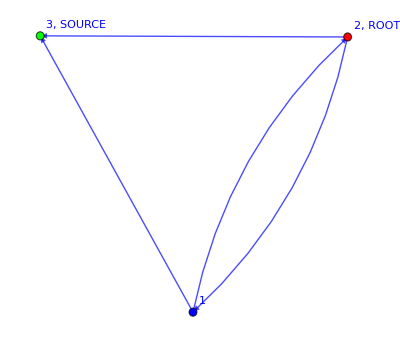

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]]
```

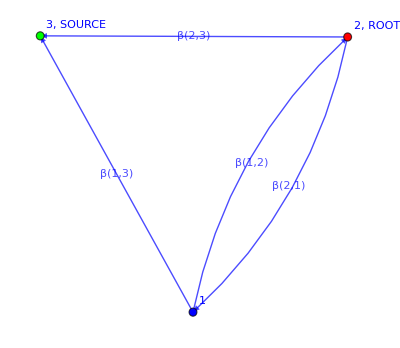

```mathematica
gLabel=MyGraph[edges,root,source,"printEdgesLabel"->True]
```

## DrawOnGraph[]

“Path” should be made of triplets whose first two elements are the initial and final vertices respectively, while the last is the color of this edge

```mathematica
Clear[DrawOnGraph];
Options[DrawOnGraph]={"drawOthers"-> True};
DrawOnGraph[graph_,path__,OptionsPattern[]]:=Module[{locEdges,locPathStyle={},locRoot,locSource,i},
locEdges = EdgeList@graph;
locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

For[i=1, i<=Length[path],i++,
AppendTo[locPathStyle,{path[[i,1]]->path[[i,2]]->path[[i,3]]}];
(*Print[locPathStyle]*)
];
If[OptionValue["drawOthers"],
(*True*)Graph[locEdges,EdgeStyle->Flatten@{locPathStyle,Blue}, VertexLabels->{locRoot->ToString[locRoot]",ROOT",locSource->ToString[locSource]",SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"],
(*False*)Graph[locEdges,EdgeStyle->Flatten@{locPathStyle,White}, VertexLabels->{locRoot->ToString[locRoot]",ROOT",locSource->ToString[locSource]",SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"]
]
]
```

### Usage example of DrawOnGraph[]

“path” should be an ordered list of pairs of vertices, i.e. edges, that form the desired Laplacian RW

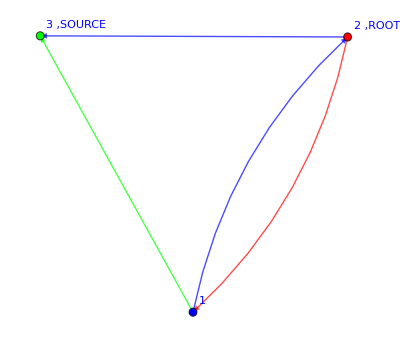

```mathematica
path1={{2,1,Red},{1,3,Green}};
DrawOnGraph[g,path1]
```

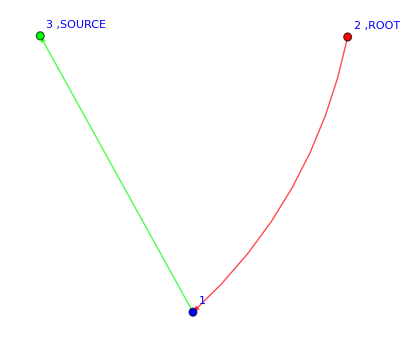

```mathematica
DrawOnGraph[g,path1,"drawOthers"->False]
```

## DrawFromExpression[]

```mathematica
Clear[DrawFromExpression];
Options[DrawFromExpression]={"graph"->g,"drawOthers"->False};

DrawFromExpression[exp_,OptionsPattern[]]:=Module[{terms,graphs={},i},
terms=exp//.R[a_,b_,c_]^n_->R[a,b,c]//Expand;
terms=List @@ (terms+Zeta[3]);
terms=terms//.β[__]->1;
terms=DeleteElements[terms,{Zeta[3]}];
terms=Outer[List,terms];
terms=terms//.Times->List;
terms=monoFlatten@@@terms;
terms=terms//.R[a_,b_,c_]->{a,b,c};
(*For[i=1,i<=Length[terms],i++,
terms[[i]]=DeleteElements[terms[[i]],{a_?NumericQ}];
];*)
Print[terms];

For[i=1,i<=Length[terms],i++,
AppendTo[graphs,DrawOnGraph[OptionValue["graph"],terms[[i,2;;]],"drawOthers"->OptionValue["drawOthers"]]];
Print[graphs[[i]]];
Print[Weight ==terms[[i,1]]];
];
]
```

## AugmentedGraph[]

This is useful to compute the total incoming current from the source towards the DLA cluster/Tree. WE MUST ADD THE EDGE FROM THE OLD SOURCE TO THE NEW SOURCE, AS WELL AS ALLOW THE EDGES FROM THE OLD SOURCE TO THE NEIGHBORS

```mathematica
Clear[AugmentedGraph];
AugmentedGraph[graph_]:=Module[{locVertices,locEdges,locPathStyle={},locRoot,locSource,newSource,oldSourceNeighbors,graphPlus,i},

locVertices = VertexList@graph;
locEdges = EdgeList@graph/.DirectedEdge->List;
locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

newSource=locVertices[[-1]]+1;

(*Add the edge from the oldSource to the newSource*)
AppendTo[locEdges,{locSource,newSource}];

(*Add all the edges from the oldSource to its neighbors*)
oldSourceNeighbors=Select[locEdges, #[[2]]==locSource &];

For[i=1,i<=Length[oldSourceNeighbors],i++,
AppendTo[locEdges,{locSource,oldSourceNeighbors[[i,1]]}]
];

graphPlus =MyGraph[locEdges,locRoot,newSource,"undirected"->False][[1]];

Return[{graphPlus,locSource,newSource}]
]
```

#### Usage example of AugmentedGraph[]

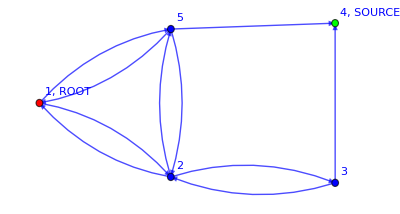

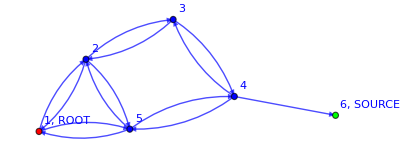
{-Graphics-,4,6}

```mathematica
g=myFavoriteGraph
AugmentedGraph[g]
```

# Automated solver of the Laplace equation

## LaplaceEqSolver[]

```mathematica
Clear[LaplaceEqSolver];
Options[LaplaceEqSolver]={"BC"->{{},{}} , "selectSolution"->0};

LaplaceEqSolver[graph_,OptionsPattern[]]:=Module[{locVertices,locWeights,totWeights,locRoot,locSource,locBC,equations,variables={},x,solution},
Clear[Φ];

locVertices = VertexList@graph;
locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

locBC=OptionValue["BC"];

AppendTo[locBC[[1]],Φ[locSource]== 1];
AppendTo[locBC[[1]],Φ[locRoot]==0];

AppendTo[locBC[[2]],locSource];
AppendTo[locBC[[2]],locRoot];

equations =locBC[[1]] ;

For[x=1,x<=Length[locVertices],x++,
AppendTo[variables,Φ[x]];
If[MemberQ[locBC[[2]],x],Continue[]];
AppendTo[equations, Φ[x]==FullSimplify[Sum[locWeights[[x,y]]/totWeights[[x]] Φ[y],{y,Length[locVertices]}]]]];
(*Print[equations];
Print[variables];*)
solution=Flatten@Solve[equations,variables]/.Rule->List;

If[OptionValue["selectSolution"]!=0,(*True*)
solution=Select[solution,#[[1]]==Φ[OptionValue["selectSolution"]] &][[1,2]]
];

Return[solution]
]
```

### Usage example of LaplaceEqSolver[]

“boundaryConditions” should be a 2d list with the boundary conditions given as a first list, e.g. {ϕ[1] == 1, ϕ[2] == 0}. The second list must contain the vertices in the boundary, e.g. {1, 2}

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];

BC={{Φ[3]==1,Φ[2]==0},{3,2}};
path1={{2,1},{1,3}};
sol=LaplaceEqSolver[g]
Select[sol,#[[1]]==Φ[path1[[1,2]]] &][[1,2]];

sol=LaplaceEqSolver[g,"selectSolution"->1]
```

{{Φ[1],(β_(1,3))/(β_(1,2)+β_(1,3))},{Φ[2],0},{Φ[3],1}}

(β_(1,3))/(β_(1,2)+β_(1,3))

Let’s keep the value at the source general. The idea is that we want to use it to impose the normalization such that ϕ are already properly normalized for being transition probabilities.

```mathematica
BC={{Φ[3]==Zeta[3],Φ[2]==0},{3,2}};
path1={{2,1},{1,3}};
sol=LaplaceEqSolver[g,BC,Φ]
```

{{Φ[1],(Zeta[3] β[1,3])/(β[1,2]+β[1,3])},{Φ[2],0},{Φ[3],Zeta[3]}}

As you can see from the previous example, the source’s value appear at numerator. So, we need to instead take its inverse. THE CRUCIAL THING IS THAT IT IS EXTREMELY EASY TO TAKE THE INVERSE OF A NUMBER, COMPARED TO THE INVERSE OF AN EXPECTATION VALUE!!!!!

## LaplacianRW[]

Computes the probability of a given Laplacian RW

```mathematica
Clear[LaplacianRW];
Options[LaplacianRW]={"draw"->False};
LaplacianRW[graph_,path__,OptionsPattern[]]:=Module[{locSource,locRoot,locWeights,locVertices,denominator,prob=1},
locWeights=WeightedAdjacencyMatrix[graph]//Normal;
locVertices=VertexList@graph;
locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];
If[locRoot =!= path[[1,1]], Print["####  WRONG ROOT  ####"]; Return[NULL]];
If[locSource =!= path[[-1,2]], Print["####  WRONG SOURCE  ####"];Return[NULL]];

Module[{locBC={{},{}},ϕ,i,ϕsol},
AppendTo[locBC[[1]],ϕ[locSource]==1];
AppendTo[locBC[[2]],locSource];
For[i=1,i<=Length[path],i++,
AppendTo[locBC[[1]],ϕ[path[[i,1]]]==0];
AppendTo[locBC[[2]],path[[i,1]]];

(*Print[locBC]*);

ϕsol=LaplaceEqSolver[graph,locBC,ϕ];
(*Print[ϕsol]*);

denominator=Sum[locWeights[[path[[i,1]],y]]*Select[ϕsol,#[[1]]==ϕ[y] &][[1,2]],{y,Length[locVertices]}];
(*Print[denominator]*);


Print["#####  Transition probability "<>ToString[path[[i,1]]]<>" to "<>ToString[path[[i,2]]]<>"  #####"];
Print[(locWeights[[path[[i,1]],path[[i,2]]]]*Select[ϕsol,#[[1]]==ϕ[path[[i,2]]] &][[1,2]])/denominator/.β[_,_]->1//FullSimplify];

prob*=(locWeights[[path[[i,1]],path[[i,2]]]]*Select[ϕsol,#[[1]]==ϕ[path[[i,2]]] &][[1,2]])/denominator//FullSimplify;
Clear[ϕsol];
]
];
If[OptionValue["draw"],Print[DrawOnGraph[graph,path]]];
Return[prob]
]
```

Let’s write a modified LaplacianRW function that uses the normalization trick to normalize the transition probability. The only problem is the first step, so we compute it separately using the standard procedure.

(****************************************************************************************************************************)
NOT SO EASY, PLEASE LOOK AT IT MORE CAREFULLY. IN PARTICULAR WE NEED TO DIVIDE BY THE PARTITION FUNCTION!!!!!
So, we need to use a partition function calculator. I am trying to implement it in another notebook following Kay’s advice. But I am not able to reproduce it. So, since its program is just an optimization, I will use mine and think about how to improve it in the future.
(****************************************************************************************************************************)

```mathematica
Clear[LaplacianRW2];
Options[LaplacianRW2]={"draw"->False,"print"->False};

LaplacianRW2[graph_,path__,OptionsPattern[]]:=Module[{locSource,locRoot,locWeights,totWeights,locVertices,denominator,prob=1, Z,numerator},
locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@graph;

locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

If[locRoot =!= path[[1,1]], Print["####  WRONG ROOT  ####"]; Return[NULL]];
If[locSource =!= path[[-1,2]], Print["####  WRONG SOURCE  ####"];Return[NULL]];

Module[{locBC={{},{}},ϕ,i=1,j,ϕsol},
AppendTo[locBC[[1]],ϕ[locSource]==1];
AppendTo[locBC[[2]],locSource];

AppendTo[locBC[[1]],ϕ[path[[i,1]]]==0];
AppendTo[locBC[[2]],path[[i,1]]];

ϕsol=LaplaceEqSolver[graph,locBC,ϕ];
(*Print[ϕsol]*);

denominator=Sum[locWeights[[path[[i,1]],y]]*Select[ϕsol,#[[1]]==ϕ[y] &][[1,2]],{y,Length[locVertices]}];
(*Print[denominator]*);

numerator=locWeights[[path[[i,1]],path[[i,2]]]] * Select[ϕsol,#[[1]]==ϕ[path[[i,2]]] &][[1,2]]//FullSimplify;

prob*=numerator/denominator//FullSimplify;

Print["#####  Transition probability "<>ToString[path[[i,1]]]<>" to "<>ToString[path[[i,2]]]<>"  #####"];
Print[prob/.β[_,_]->1//FullSimplify];

Clear[ϕsol,locBC];

For[i=2,i<=Length[path],i++,
(*We need to solve it once with standard BCs at the previous step, i.e. ϕ[locSource]==1*)
locBC={{ϕ[locSource]==1},{locSource}};

For[j=1,j<=i-1,j++,
AppendTo[locBC[[1]],ϕ[path[[j,1]]]==0];
AppendTo[locBC[[2]],path[[j,1]]]
]

(*Print[locBC]*);

Z=VertexAssignment[graph, "excludedVertices"->locBC[[2]]];
Z=ExpectationValue[Z];

If[OptionValue["print"],
Print["#####  Previous Partition Function  #####"];
Print[Z]
];

ϕsol=LaplaceEqSolver[graph,locBC,ϕ];
(*Print[ϕsol];*)

denominator=1/Z*Select[ϕsol,#[[1]]==ϕ[path[[i,1]]] &][[1,2]]//FullSimplify;

Clear[ϕsol, locBC];


(*Then we need to solve it again with updated BC at the current step*)
locBC={{ϕ[locSource]==denominator^-1},{locSource}};

For[j=1,j<=i,j++,
AppendTo[locBC[[1]],ϕ[path[[j,1]]]==0];
AppendTo[locBC[[2]],path[[j,1]]]
]

(*Print[locBC]*);

Z=VertexAssignment[graph, "excludedVertices"->locBC[[2]]];
Z=ExpectationValue[Z];

If[OptionValue["print"],
Print["#####  Current Partition Function  #####"];
Print[Z]
];

ϕsol=LaplaceEqSolver[graph,locBC,ϕ];
(*Print[ϕsol]*);

Print["#####  Transition probability "<>ToString[path[[i,1]]]<>" to "<>ToString[path[[i,2]]]<>"  #####"];
Print[1/Z*locWeights[[path[[i,1]],path[[i,2]]]]/totWeights[[path[[i,1]]]]*Select[ϕsol,#[[1]]==ϕ[path[[i,2]]] &][[1,2]]/.β[_,_]->1//FullSimplify];

prob*=1/Z*locWeights[[path[[i,1]],path[[i,2]]]]/totWeights[[path[[i,1]]]]*Select[ϕsol,#[[1]]==ϕ[path[[i,2]]] &][[1,2]]//FullSimplify;

Clear[ϕsol,locBC];
]
];
If[OptionValue["draw"],Print[DrawOnGraph[graph,path]]];
Return[prob]
]
```

### Usage example of LaplacianRW[] &LERWtransitionProb[]

“path” should be an ordered list of pairs of vertices, i.e. edges, that form the desired Laplacian RW.
If “draw” is true, then draw the path

Simple cases first

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];

path1={{2,1},{1,3}};
LaplacianRW[g,{{2,1},{1,3}}](*/.β[_,_]->1*)
```

Part::partd: Part specification ()⟦1⟧ is longer than depth of object.

Part::partd: Part specification ϕ$21364⟦1⟧ is longer than depth of object.

Part::partw: Part 1 of LaplaceEqSolver[] does not exist.

Part::partd: Part specification ()⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 1 of LaplaceEqSolver[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

#####  Transition probability 2 to 1  #####

1/2

#####  Transition probability 1 to 3  #####

1/2

((LaplaceEqSolver[]⟦1,2⟧)^2 β_(1,3) β_(2,1))/((LaplaceEqSolver[]⟦1,2⟧ β_(1,2)+LaplaceEqSolver[]⟦1,2⟧ β_(1,3)) (LaplaceEqSolver[]⟦1,2⟧ β_(2,1)+LaplaceEqSolver[]⟦1,2⟧ β_(2,3)))

```mathematica
(β[1,3] β[2,1])/((β[1,2]+β[1,3]) ((β[1,3] β[2,1])/(β[1,2]+β[1,3])+β[2,3]))//FullSimplify
```

(β[1,3] β[2,1])/(β[1,2] β[2,3]+β[1,3] (β[2,1]+β[2,3]))

```mathematica
%//FullSimplify
```

(β[1,3] β[2,1])/(β[1,2] β[2,3]+β[1,3] (β[2,1]+β[2,3]))

```mathematica
(*Correct!!*)
```

```mathematica
VertexAssignment[g,"excludedVertices"->{2,3}]
LERWtransitionProb[g,path1]
```

(1+χ[3,i_s]) (1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3]))

#####  Transition probability 2 to 1  #####

1/3

#####  Transition probability 1 to 3  #####

1

(β[1,3] β[2,1])/(β[1,2] β[2,3]+β[1,3] (β[2,1]+β[2,3]))

```mathematica
(*Correct!!*)
```

Let’s try with another example, i.e. my favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
PathFinder[myFavoriteGraph]
```

{{{1,2},{2,3},{3,4}},{{1,2},{2,5},{5,4}},{{1,5},{5,2},{2,3},{3,4}},{{1,5},{5,4}}}

#####  Transition probability 1 to 2  #####

5/11

#####  Transition probability 2 to 3  #####

3/5

#####  Transition probability 3 to 4  #####

1

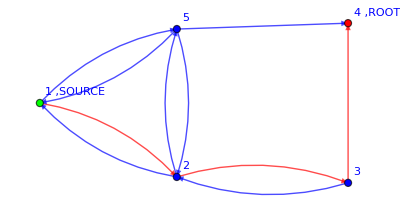

3/11

```mathematica
path2={{1,2},{2,3},{3,4}};
LaplacianRW[myFavoriteGraph,path2,"draw"->True]/.β[_,_]->1
```

```mathematica
LERWtransitionProb[myFavoriteGraph,path2]/.β[_,_]->1
```

#####  Transition probability 1 to 2  #####

5/11

#####  Transition probability 2 to 3  #####

3/5

#####  Transition probability 3 to 4  #####

1

3/11

```mathematica
(*Correct!!!*)
```

## PathFinder[]

```mathematica
Clear[PathFinder];

PathFinder[graph_]:=Module[{pathList={{}}},
Step[subgraph_]:=Module[{locEdges,locVertices,locWeights,locRoot,locSource,locMoves,newEdges, newRoot,smallerGraph,i},
locEdges = EdgeList@subgraph/.DirectedEdge->List;
locVertices=VertexList@subgraph;
If[Length[locVertices]==1,Return[NULL]];
locWeights=WeightedAdjacencyMatrix[subgraph]//Normal;
locRoot = 
 Select[(List@@@PropertyValue[subgraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[subgraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];
locMoves=Select[locEdges,#[[1]]==locRoot &][[All]];

(*Print["###  LocMoves  ####"];
Print[locMoves];*);

For[i=1, i<=Length[locMoves],i++,

If[i ==Length[locMoves],
(*True*)If[locMoves[[i,2]]==locSource,
 (*Ture*)pathList=Append[pathList[[2;;]],Append[pathList[[1]],locMoves[[i]]]]; Continue[],
 (*False*)pathList=Prepend[pathList[[2;;]],Append[pathList[[1]],locMoves[[i]]]]
],
(*False*)
If[locMoves[[i,2]]==locSource,
 (*True*)pathList=Append[pathList,Append[pathList[[1]],locMoves[[i]]]];Continue[],
 (*False*)pathList=Prepend[pathList,Append[pathList[[1]],locMoves[[i]]]]
]];

(*Print["###  pathList  ####"];
Print[pathList];*);

newEdges=Select[locEdges,#[[1]]=!=locRoot && #[[2]]=!=locRoot &][[All]];
newRoot = locMoves[[i,2]];
If[Length[newEdges] <= 0,Continue[]];
smallerGraph=MyGraph[newEdges,newRoot,locSource,"undirected"->False][[1]];

(*Print[smallerGraph];*);

Step[smallerGraph]
]
];

Step[graph];
Return[pathList]
]
```

### Usage example of PathFinder[]

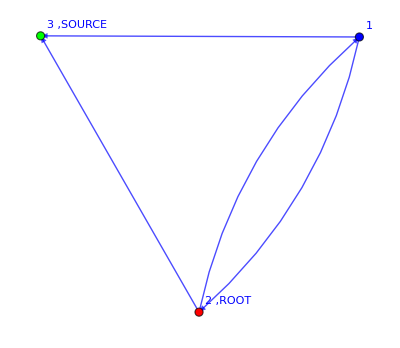

{{{2,1},{1,3}},{{2,3}}}

```mathematica
g
PathFinder[g]
```

So

```mathematica
(*Last step available*)
v=Prepend[v[[2;;]],Append[v[[1]],step0]]
```

```mathematica
(*Multiple steps available*)
v=Prepend[v,Append[v[[1]],step1]]
```

```mathematica
(*Source reached with last step available*)
v=Append[v[[2;;]],Append[v[[1]],step2]]
```

```mathematica
(*Source reached with multiple steps available*)
v=Append[v,Append[v[[1]],step2]]
```

Test

```mathematica
Clear[a];
(*The first position is the one we are gonna update*)
v={{}}
rooot=a;
v=Prepend[v[[2;;]],Append[v[[1]],rooot]]
step0=b;(*If b is the only step available, then we do not need a copy of v*)
v=Prepend[v[[2;;]],Append[v[[1]],step0]]
step1=c;(*Imagine we can now move to c or c2. We then need a copy of v to be able to come back at this bifurcation*)
v=Prepend[v,Append[v[[1]],step1]]
step2=d;(*If d reaches the source, then add it to the end*)
v=Append[v,Append[v[[1]],step2]]
step2bis=d2;(*If d2 is the only step available, then we do not need a copy of v*)
v=Prepend[v[[2;;]],Append[v[[1]],step2bis]]
step3=e;(*If e reaches the source, and is the only step available, add it at the end without copying v*)
v=Append[v[[2;;]],Append[v[[1]],step3]]
```

{{}}

{{a}}

{{a,b}}

{{a,b,c},{a,b}}

{{a,b,c},{a,b},{a,b,c,d}}

{{a,b,c,d2},{a,b},{a,b,c,d}}

{{a,b},{a,b,c,d},{a,b,c,d2,e}}

## AllLaplacianRWs[]

```mathematica
Clear[AllLaplacianRWs]

Options[AllLaplacianRWs]={"draw"->False,"print"->False};

AllLaplacianRWs[graph_,OptionsPattern[]]:=Module[{possibleLRW,i,probabilityLRW={}},
possibleLRW=PathFinder[graph];
For[i=1, i<= Length[possibleLRW],i++,
AppendTo[probabilityLRW,LaplacianRW[graph,possibleLRW[[i]],OptionValue["draw"]]];
If[OptionValue["print"],Print[i,") Laplacian RW ",possibleLRW[[i]]," with probability " ,probabilityLRW[[i]]]
]
];
Return[{possibleLRW,probabilityLRW}]
]
```

### Usage example of AllLaplacianRWs[]

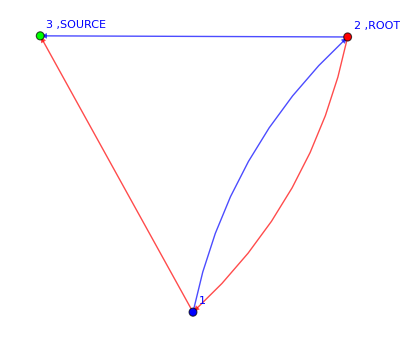

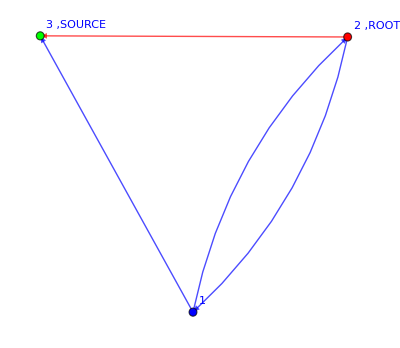

{{{{2,1},{1,3}},{{2,3}}},{(β[1,3] β[2,1])/((β[1,2]+β[1,3]) ((β[1,3] β[2,1])/(β[1,2]+β[1,3])+β[2,3])),β[2,3]/((β[1,3] β[2,1])/(β[1,2]+β[1,3])+β[2,3])}}

```mathematica
AllLaplacianRWs[g,"draw"->True]
```

## Application to “my favorite” graph: CORRECT!

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

-Graphics-

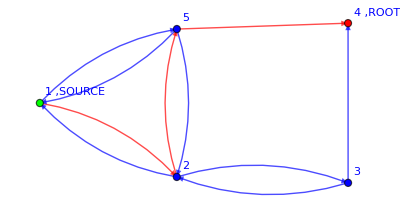

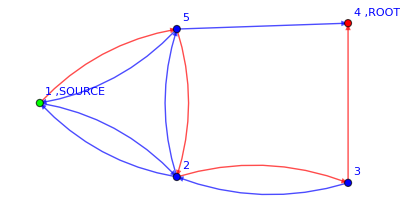

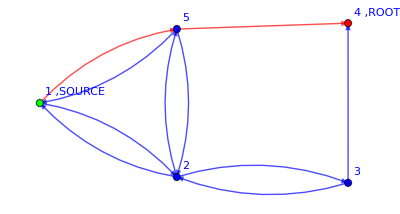

{{{{1,2},{2,3},{3,4}},{{1,2},{2,5},{5,4}},{{1,5},{5,2},{2,3},{3,4}},{{1,5},{5,4}}},{3/11,2/11,1/11,5/11}}

```mathematica
AllLaplacianRWs[myFavoriteGraph,"draw"->True]/.β[_,_]->1
```

# LERW&DLA

## monoFlatten[]

```mathematica
Clear[monoFlatten];
(*monoFlatten[a_?NumericQ]:={};*)
monoFlatten[a_]:={a};
monoFlatten[{a__}]:={{a}};
monoFlatten[{a__,b__}]:={a,b};
```

## ExtractPaths[]

```mathematica
(*To extract the paths and their weights from the expression of an expectation value*)
```

```mathematica
Clear[ExtractPaths];
ExtractPaths[exp_]:=Module[{terms,paths={},i},

terms=exp//Expand;
terms=List @@Collect[terms,R[__,Red]];
terms=Outer[List,terms];

For[i=1,i<=Length[terms],i++,
If[MatchQ[terms[[i,1]],R[__,Red]*A_],
AppendTo[paths,terms[[i]]]
]
];
terms=paths//.R[__,Blue]->1//FullSimplify;

Return[terms]
]
```

#### Usage example of ExtractPaths[]

```mathematica
exp=(1-(Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,2,RGBColor[0, 0, 1]] Subscript[β, 2,3] Subscript[β, 3,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]))+(Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,4,RGBColor[0, 0, 1]] Subscript[β, 1,2] Subscript[β, 2,3] Subscript[β, 3,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]))-(Subscript[R, 2,5,RGBColor[0, 0, 1]] Subscript[R, 5,2,RGBColor[0, 0, 1]] Subscript[β, 2,5] Subscript[β, 5,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))+(Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,4,RGBColor[0, 0, 1]] Subscript[R, 5,2,RGBColor[0, 0, 1]] Subscript[β, 1,5] Subscript[β, 2,3] Subscript[β, 3,4] Subscript[β, 5,2])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))+(Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[0, 0, 1]] Subscript[β, 1,5] Subscript[β, 5,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))+(Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[0, 0, 1]] Subscript[R, 5,4,RGBColor[0, 0, 1]] Subscript[β, 1,2] Subscript[β, 2,5] Subscript[β, 5,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))-(Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,2,RGBColor[0, 0, 1]] Subscript[R, 5,4,RGBColor[0, 0, 1]] Subscript[β, 1,5] Subscript[β, 2,3] Subscript[β, 3,2] Subscript[β, 5,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4])));ExtractPaths[exp]
```

{{(R_(1,2,RGBColor[1, 0, 0]) β_(1,2) (β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4))))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))},{(R_(1,5,RGBColor[1, 0, 0]) β_(1,5) ((β_(2,1)+β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,2)+β_(5,4))))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))}}

## Vertex rules and VertexAssignment[]

The vertices are where the interaction takes place in the field theory.

```mathematica
Clear[V];
V[1]:=1;
(*V[0]:=0;*)
V'[a_]:=1
```

```mathematica
Clear[VertexAssignment];
Options[VertexAssignment]={"system"->"LERW","print"->False,"excludedVertices"->{},"sourceBC"->1};

VertexAssignment[graph_,OptionsPattern[]]:=Module[{locVertices,locWeights,totWeights,locSource,action,x,y},
Clear[i];
locVertices=VertexList@graph;
locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

(*LERW*)
If[OptionValue["system"]=="LERW",
If[OptionValue["print"],Print["#####   "<>OptionValue["system"]<>"   #####"]];
action = Product[ If[totWeights[[x]]===0 || MemberQ[OptionValue["excludedVertices"],x],1,V[(1+ Sum[locWeights[[x,y]]/totWeights[[x]] χs[y,Subscript[i, x]]χ[x,Subscript[i, x]],{y,Length[locVertices]}] ) ]],{x,Length[locVertices]}];
action*=V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[i, s]])];(*This is the BC*)
Return[action]];

(*DLA*)
If[OptionValue["system"]=="DLA",If[OptionValue["print"],Print["#####   "<>OptionValue["system"]<>"   #####"]];
Return[
Product[ If[totWeights[[x]]===0 || MemberQ[OptionValue["excludedVertices"],x],1,V[(1+ Product[1+locWeights[[x,y]]/totWeights[[x]] χs[y,Subscript[i, x]],{y,Length[locVertices]}] χ[x,Subscript[i, x]]+ Sum[locWeights[[x,y]]/totWeights[[x]] ϕs[y,Subscript[j, x]]ϕ[x,Subscript[j, x]],{y,Length[locVertices]}])] ],{x,Length[locVertices]}]
]]
]
```

### Usage example of VertexAssignment[]

```mathematica
Z=VertexAssignment[g[[1]],"system"->"LERW"]
```

(1+χ[4,i_s]) (1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])) (1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,i_2] χs[4,i_2])/(β[2,1]+β[2,4])) (1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4]))

```mathematica
VertexAssignment[g[[1]],"system"->"LERW","excludedVertices"->{1}]
```

(1+χ[4,i_s]) (1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,i_2] χs[4,i_2])/(β[2,1]+β[2,4])) (1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4]))

## δrules

```mathematica
ClearAll[Σδrule]
Σδrule={δ[a_,b_]^n_/;(!NumericQ[b]&& !MatchQ[b,Subscript[1, __]]):>δ[a,b]^(n-2)δ[a,a],
δ[b_,a_]δ[c_,b_]/;(!NumericQ[b] && !MatchQ[b,Subscript[1, __]]):>δ[c,a],
δ[a_,b_]δ[c_,b_]/;(!NumericQ[b]&& !MatchQ[b,Subscript[1, __]]):>δ[a,c],
δ[a_,a_]/;(MatchQ[a,Subscript[i, __]])/;(a=!=Subscript[i, s]):>n,
δ[a_,a_]/;(MatchQ[a,Subscript[k, _]]):>1};
```

```mathematica
ClearAll[δruleExternal]
δruleExternal={δ[a_,a_]/;(NumericQ[a] || a==Subscript[i, s] || MatchQ[a,Subscript[j, __]] || MatchQ[a,Subscript[1, __]]||MatchQ[a,Subscript[k, _]]):>1,
δ[a_,b_]/;(NumericQ[a] ||MatchQ[a,Subscript[k, _]]|| MatchQ[a,Subscript[j, __]]|| MatchQ[a,Subscript[1, _]])/;(a=!=b):>0,
δ[a_,b_]/;(NumericQ[b] ||MatchQ[b,Subscript[k, _]]|| MatchQ[b,Subscript[j, __]]|| MatchQ[b,Subscript[1, _]])/;(a=!=b):>0 };
```

### Usage examples of the δrules

```mathematica
δ[b,a]δ[c,b]/.Σδrule
```

δ[c,a]

```mathematica
δ[b,a]δ[a,b]//.Σδrule
```

n

```mathematica
δ[b,a]δ[c,a]δ[c,b]//.Σδrule
```

n

```mathematica
δ[1,i]δ[i,1]//.Σδrule//.δruleExternal
```

1

```mathematica
δ[1,i]δ[i,2]//.Σδrule//.δruleExternal
```

0

```mathematica
δ[1,i]δ[i,1]δ[a,b]δ[a,b]//.Σδrule//.δruleExternal
```

δ[a,a]

```mathematica
δ[Subscript[k, 1],Subscript[k, 1]]//.Σδrule
```

m

```mathematica
δ[Subscript[i, 1],Subscript[i, 1]]//.Σδrule
```

n

```mathematica
δ[Subscript[j, -1],Subscript[j, -1]]//.δruleExternal
```

1

```mathematica
δ[Subscript[k, -1],Subscript[k, -1]]//.δruleExternal
```

1

```mathematica
δ[Subscript[1, 1],Subscript[1, -1]]δ[Subscript[1, 1],Subscript[1, -1]]//.Σδrule
```

δ[1_1,1_-1]^2

## Operator “vertices” rules

```mathematica
Clear[Op];
Op[1]:=1;
Op[0]:=0;
Op'[_]:=1
```

## WickContraction[]

NOW IT WORKS, but only up to a 2-point function!!!!!!!!

```mathematica
Clear[WickContraction];
Options[WickContraction]={"print"->False,"fields"->{χ}, "endTime"->0(*It is set to 0 for the statical case*)};

WickContraction[A_ +B_,OptionsPattern[]]:=WickContraction[A,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"]]+WickContraction[B,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"]];

WickContraction[A_ +B__+C__,OptionsPattern[]]:=WickContraction[A,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"]]+WickContraction[B+C,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"]];

WickContraction[A_?NumericQ,OptionsPattern[]]:=A;


(*################################################################################
									Expectation Values                             
##############################################################################*)
(*There are two possible contributions for each field: 1) it is not contracted: χ->0; 2) it is contracted*)
WickContraction[Op[A_] *B_, OptionsPattern[]]:=Module[{locFields={}, starFields={}, deltaFields={},deltaStarFields={},contributions=0,z,zTemp,κ,j,l,timeIndex},
z=Op[A]B;

Print["###################  Operator found  ##################"];


locFields=OptionValue["fields"];

For[l=1,l<=Length[locFields],l++,
AppendTo[starFields, ToExpression[ToString[locFields[[l]]] <> "s"]];
AppendTo[deltaFields, ToExpression["δ"<>ToString[locFields[[l]]] ]];
AppendTo[deltaStarFields,ToExpression["δ"<> ToString[starFields[[l]]] ]];
];(*End of loop to define the fields*)

If[OptionValue["print"],
Print[locFields,starFields,deltaFields,deltaStarFields];
];

For[timeIndex=0,timeIndex<=(OptionValue["endTime"]),timeIndex++,

(*
If[timeIndex==0, 
(*TRUE*)If[OptionValue["endTime"]==0,timeIndex++,Continue[]],
(*FALSE*)z=z//.f_[x_,Subscript[t, timeIndex],a_]->f[x,a];
];*)

If[OptionValue["print"],
Print["###################  Time "<> ToString[timeIndex+1]<>"  ##################"];
Print[z]
];

If[OptionValue["endTime"]!=0,
(*TRUE*)z=z//.f_[x_,Subscript[t, (timeIndex+1)],a_]->f[x,a]
];

(*Start of loop over fields*)
For[l=1,l<=Length[locFields],l++,

(*Start of loop over space*)
For[j=1,j<=100,j++,
(*First contribution*)
zTemp=z//.locFields[[l]][j,a_]->0//.starFields[[l]][j,a_]->0;
If[zTemp-z=!=0,
contributions=zTemp;
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": First contribution ####"];
Print[contributions]]
];

(*Second contribution*)
zTemp=z/. locFields[[l]][j,a_]->locFields[[l]][j,a]+κ *deltaFields[[l]][j,a];
If[zTemp-z=!=0,
z=D[zTemp,κ]/.κ->0;
];

zTemp=z/. starFields[[l]][j,a_]->starFields[[l]][j,a]+κ *deltaStarFields[[l]][j,a];
If[zTemp-z=!=0,
z=D[zTemp,κ]/.κ->0;
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": second contribution ####"];
Print[z]
]
];

z=Expand[z];
zTemp=z//.deltaFields[[l]][j,a_]*deltaStarFields[[l]][j,b_](*/;(!NumericQ[a*b]):>*)->δ[a,b];

If[zTemp-z=!=0,
If[OptionValue["print"],
Print["#### Contraction "<>ToString[j]<>" ####"];
Print[z=zTemp]
]
];
z=zTemp/.deltaFields[[l]][j,a_]->0/.deltaStarFields[[l]][j,b_]->0;


If[contributions-z=!=0,
contributions+=z;
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": total contribution ####"];
Print[contributions]]
];

z=contributions;
contributions=0;

];(*End of loop over space*)

z=z/.locFields[[l]][x_,a_]->0;
z=z/.starFields[[l]][x_,a_]->0;

];(*End of loop over fields*)

(*
For[l=1,l<=Length[locFields],l++,
z=z/.locFields[[l]][x_,a_]->0;
z=z/.starFields[[l]][x_,a_]->0;
];*)

z=z//.Σδrule;
];(*End of loop over time*)

Return[z]
];


(*################################################################################
									Partition Function                             
##############################################################################*)
(*There are two possible contributions for each field: 1) it is not contracted: χ->0; 2) it is contracted*)

WickContraction[V[A_] *B_, OptionsPattern[]]:=Module[{locFields={}, starFields={}, deltaFields={},deltaStarFields={},contributions=0,z,zTemp,κ,j,l,timeIndex},
z=V[A]B;

Print["###################  Partition Function  ##################"];


locFields=OptionValue["fields"];

For[l=1,l<=Length[locFields],l++,
AppendTo[starFields, ToExpression[ToString[locFields[[l]]] <> "s"]];
AppendTo[deltaFields, ToExpression["δ"<>ToString[locFields[[l]]] ]];
AppendTo[deltaStarFields,ToExpression["δ"<> ToString[starFields[[l]]] ]]
];(*End of loop to define the fields*)

If[OptionValue["print"],
Print[locFields,starFields,deltaFields,deltaStarFields]
];

For[timeIndex=0,timeIndex<=(OptionValue["endTime"]),timeIndex++,

(*If[timeIndex==0, 
(*TRUE*)If[OptionValue["endTime"]==0,timeIndex++,Continue[]],
(*FALSE*)z=z//.f_[x_,Subscript[t, timeIndex],a_]->f[x,a];
];*)

If[OptionValue["print"],
Print["###################  Time "<> ToString[timeIndex+1]<>"  ##################"];
Print["Z before"];
Print[z]
];

If[OptionValue["endTime"]!=0,
(*TRUE*)z=z//.f_[x_,Subscript[t, (timeIndex+1)],a_]->f[x,a]
];

If[OptionValue["print"],
Print["Z After"];
Print[z]
];

(*Start of loop over fields*)
For[l=1,l<=Length[locFields],l++,

(*Start of loop over space*)
For[j=1,j<=100,j++,

(*First contribution*)
zTemp=z//.locFields[[l]][j,a_]->0//.starFields[[l]][j,a_]->0;
If[zTemp-z=!=0,
contributions=zTemp;
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": First contribution ####"];
Print[contributions]]
];

(*Second contribution*)
zTemp=z/. locFields[[l]][j,a_]->locFields[[l]][j,a]+κ *deltaFields[[l]][j,a];
If[zTemp-z=!=0,
z=D[zTemp,κ]/.κ->0;
];

zTemp=z/. starFields[[l]][j,a_]->starFields[[l]][j,a]+κ *deltaStarFields[[l]][j,a];
If[zTemp-z=!=0,
z=D[zTemp,κ]/.κ->0;
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": second contribution ####"];
Print[z]
]
];

z=Expand[z];
zTemp=z//.deltaFields[[l]][j,a_]*deltaStarFields[[l]][j,b_](*/;(!NumericQ[a*b]):>*)->δ[a,b];

If[zTemp-z=!=0,
If[OptionValue["print"],
Print["#### Contraction "<>ToString[j]<>" ####"];
Print[z=zTemp]
]
];

z=zTemp/.deltaFields[[l]][j,a_]->0/.deltaStarFields[[l]][j,b_]->0;


If[contributions-z=!=0,
contributions+=z;
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": total contribution ####"];
Print[contributions]]
];

z=contributions;
contributions=0;

];(*End of loop over space*)

z=z/.locFields[[l]][x_,a_]->0;
z=z/.starFields[[l]][x_,a_]->0;

];(*End of loop over fields*)

(*For[l=1,l<=Length[locFields],l++,
z=z/.locFields[[l]][x_,a_]->0;
z=z/.starFields[[l]][x_,a_]->0
];*)

z=z//.Σδrule;

];(*End of loop over time*)

Return[z]
];
```

### Usage example of WickContraction[]

Simple

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source];
Z=VertexAssignment[g[[1]],"system"->"LERW"];
WickContraction[Z]/.n->-1
```

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
WickContraction[Z,"endTime"->1]/.n->-1
```

2-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

More complex example CORRECT!!

```mathematica
edges={{1,3},{1,2},{2,2},{2,3}};
root=1;
source=3;
g=MyGraph[edges,root,source];
g[[1]];
Z=VertexAssignment[g[[1]]]
WickContraction[Z]/.n->-1
```

V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,2]+β[2,3])+(β[2,2] χ[2,i_2] χs[2,i_2])/(β[2,1]+β[2,2]+β[2,3])+(β[2,3] χ[2,i_2] χs[3,i_2])/(β[2,1]+β[2,2]+β[2,3])]

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,2]+β[2,3]))-β[2,2]/(β[2,1]+β[2,2]+β[2,3])

Regular 2x2 lattice with absorption (i.e. source) at 4

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source];
g[[1]];
Z=VertexAssignment[g[[1]]]

WickContraction[Z]/.n->-1
```

V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,i_2] χs[4,i_2])/(β[2,1]+β[2,4])] V[1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4])]

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))-(β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))

## ExpectationValue[]

```mathematica
Clear[ExpectationValue];
Options[ExpectationValue]={"operator"->1,"print"->False, "fields"->{χ},"endTime"->1,"draw"->False,"graph"->g, "Rrule"->{R[__]->1}};

ExpectationValue[Z_,OptionsPattern[]]:=Module[{z,terms,graphs={},i},
If[OptionValue["operator"]===1,
(*True*)z=WickContraction[Z,
"print"->OptionValue["print"], 
"fields"->OptionValue["fields"],
"endTime"->OptionValue["endTime"]
],
(*False*)z=WickContraction[Z*Op[OptionValue["operator"]],
"print"->OptionValue["print"], 
"fields"->OptionValue["fields"],
"endTime"->OptionValue["endTime"]
]/WickContraction[Z, "fields"->OptionValue["fields"],"endTime"->OptionValue["endTime"]]
];

z=z//.δruleExternal;
z=z/.n->-1;
z=z/.m->0;

If[OptionValue["draw"],
(*True*)
z=z//.R[a_,b_,c_]^n_->R[a,b,c];
terms=List @@ (z+Zeta[3]);
terms=terms//.β[__]->1;
terms=DeleteElements[terms,{Zeta[3]}];
terms=Outer[List,terms];
terms=terms//.Times->List;
terms=monoFlatten@@@terms;
terms=terms//.R[a_,b_,c_]->{a,b,c};
(*For[i=1,i<=Length[terms],i++,
terms[[i]]=DeleteElements[terms[[i]],{a_?NumericQ}];
];*)
Print[terms];
z=z/.R[___]->1;

For[i=1,i<=Length[terms],i++,
AppendTo[graphs,DrawOnGraph[OptionValue["graph"],terms[[i,2;;]],"drawOthers"->False]];
Print[graphs[[i]]];
Print[Weight ==terms[[i,1]]];
];,

(*False*)z=z/.OptionValue["Rrule"]];

Return[z]]
```

### Usage example of ExpectationValue[]

Simple triangular graph

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source];
Z=VertexAssignment[g[[1]],"system"->"LERW"]
ExpectationValue[Z]
```

V[1+χ[3,i_s]] V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,3])+(β[2,3] χ[2,i_2] χs[3,i_2])/(β[2,1]+β[2,3])]

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

2-point function

```mathematica
ExpectationValue[Z,"operator"->χs[1,1]χ[3,1]](*/.β[__]->1*)(*Correct*)
```

###################  Operator found  ##################

(β[1,3]/(β[1,2]+β[1,3])+(β[1,2] β[2,3])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3])))/(1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3])))

Attempts

```mathematica
z=Z Op[χs[1,1]χ[3,1]]
contributions=z;

(*At 1*)
zTemp=z/. χ[1,a_]->χ[1,a]+κ *δχ[1,a];
z=D[zTemp,κ]/.κ->0;

zTemp=z/. χs[1,a_]->χs[1,a]+κ *δχs[1,a];

z=D[zTemp,κ]/.κ->0;

z=Expand[z];
zTemp=z//.δχ[1,a_]*δχs[1,b_]/;(!NumericQ[a*b]):>δ[a,b];


z=zTemp/.δχ[1,a_]->0/.δχs[1,b_]->0;

contributions+=z;
z=contributions;

(*At 2*)
zTemp=z/. χ[2,a_]->χ[2,a]+κ *δχ[2,a];
z=D[zTemp,κ]/.κ->0;

zTemp=z/. χs[2,a_]->χs[2,a]+κ *δχs[2,a];

z=D[zTemp,κ]/.κ->0;

z=Expand[z];
zTemp=z//.δχ[2,a_]*δχs[2,b_]/;(!NumericQ[a*b]):>δ[a,b];


z=zTemp/.δχ[2,a_]->0/.δχs[2,b_]->0;

contributions+=z;
z=contributions;

(*At 3*)
zTemp=z/. χ[3,a_]->χ[3,a]+κ *δχ[3,a];
z=D[zTemp,κ]/.κ->0;

zTemp=z/. χs[3,a_]->χs[3,a]+κ *δχs[3,a];

z=D[zTemp,κ]/.κ->0;

z=Expand[z];
zTemp=z//.δχ[3,a_]*δχs[3,b_]/;(!NumericQ[a*b]):>δ[a,b];


z=zTemp/.δχ[3,a_]->0/.δχs[3,b_]->0;

contributions+=z;
z=contributions;
z=z//.{χ[x_,a_]->0,χs[x_,b_]->0};
z=z//.Σδrule;
z=z//.δruleExternal;
z=z/.n->-1
```

Op[χ[3,1] χs[1,1]] V[1+χ[3,i_s]] V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,3])+(β[2,3] χ[2,i_2] χs[3,i_2])/(β[2,1]+β[2,3])]

β[1,3]/(β[1,2]+β[1,3])+(β[1,2] β[2,3])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
z=Z Op[χs[1,1]χ[3,1]]
contributions=z;

For[j=1,j<=3,j++,
(*Print["#### "<>ToString[j]<>" ####"];
Print[z]*)

zTemp=z/. χ[j,a_]->χ[j,a]+κ *δχ[j,a];
z=D[zTemp,κ]/.κ->0;

zTemp=z/. χs[j,a_]->χs[j,a]+κ *δχs[j,a];

z=D[zTemp,κ]/.κ->0;

z=Expand[z];
zTemp=z//.δχ[j,a_]*δχs[j,b_]/;(!NumericQ[a*b]):>δ[a,b];

z=zTemp/.δχ[j,a_]->0/.δχs[j,b_]->0;

contributions+=z;
z=contributions
]

z=z//.{χ[x_,a_]->0,χs[x_,b_]->0};
z=z//.Σδrule;
z=z//.δruleExternal;
z=z/.n->-1
```

Op[χ[3,1] χs[1,1]] V[1+χ[3,i_s]] V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,3])+(β[2,3] χ[2,i_2] χs[3,i_2])/(β[2,1]+β[2,3])]

β[1,3]/(β[1,2]+β[1,3])+(β[1,2] β[2,3])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

1-point function

```mathematica
Z=VertexAssignment[g[[1]],"system"->"LERW","excludedVertices"->{2,3}]

ExpectationValue[Z]
ExpectationValue[Z,"operator"->χs[1,Subscript[i, s]]]
```

V[1+χ[3,i_s]] V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])]

1

###################  Operator found  ##################

β[1,3]/(β[1,2]+β[1,3])

More complex example CORRECT!!

```mathematica
edges={{1,3},{1,2},{2,2},{2,3}};
root=1;
source=3;
g=MyGraph[edges,root,source];
g[[1]];
Z=VertexAssignment[g[[1]]]
ExpectationValue[Z]
```

V[1+χ[3,i_s]] V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,2]+β[2,3])+(β[2,2] χ[2,i_2] χs[2,i_2])/(β[2,1]+β[2,2]+β[2,3])+(β[2,3] χ[2,i_2] χs[3,i_2])/(β[2,1]+β[2,2]+β[2,3])]

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,2]+β[2,3]))-β[2,2]/(β[2,1]+β[2,2]+β[2,3])

Regular 2x2 lattice with absorption (i.e. source) at 4

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source];
g[[1]];
Z=VertexAssignment[g[[1]]]

ExpectationValue[Z]
```

V[1+χ[4,i_s]] V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,i_2] χs[4,i_2])/(β[2,1]+β[2,4])] V[1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4])]

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))-(β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
Z=VertexAssignment[myFavoriteGraph]

ExpectationValue[Z]
```

V[1+χ[4,i_s]] V[1+(β[3,2] χ[3,i_3] χs[2,i_3])/(β[3,2]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,2]+β[3,4])] V[1+(β[5,1] χ[5,i_5] χs[1,i_5])/(β[5,1]+β[5,2]+β[5,4])+(β[5,2] χ[5,i_5] χs[2,i_5])/(β[5,1]+β[5,2]+β[5,4])+(β[5,4] χ[5,i_5] χs[4,i_5])/(β[5,1]+β[5,2]+β[5,4])] V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,5])+(β[1,5] χ[1,i_1] χs[5,i_1])/(β[1,2]+β[1,5])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,3] χ[2,i_2] χs[3,i_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,5] χ[2,i_2] χs[5,i_2])/(β[2,1]+β[2,3]+β[2,5])]

1-(β[1,2] β[2,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]))-(β[2,3] β[3,2])/((β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]))-(β[1,5] β[5,1])/((β[1,2]+β[1,5]) (β[5,1]+β[5,2]+β[5,4]))-(β[1,2] β[2,5] β[5,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))+(β[1,5] β[2,3] β[3,2] β[5,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]) (β[5,1]+β[5,2]+β[5,4]))-(β[1,5] β[2,1] β[5,2])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))-(β[2,5] β[5,2])/((β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))

This can also be used for observables

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source];
g[[1]];
Z=VertexAssignment[g[[1]]]

ExpectationValue[Z]/.β[__]->1
```

V[1+χ[4,i_s]] V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,i_2] χs[4,i_2])/(β[2,1]+β[2,4])] V[1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4])]

1/2

Two-point function OK

```mathematica
ExpectationValue[Z,"operator"->1]/.β[__]->1
0
Z Op[χs[1,1]χ[4,1]]
ExpectationValue[Z,"operator"->χs[1,1]χ[4,1],"print"->False](*/.β[__]->1*)
```

1/2

0

Op[χ[4,1] χs[1,1]] V[1+χ[4,i_s]] V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,i_2] χs[4,i_2])/(β[2,1]+β[2,4])] V[1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4])]

###################  Operator found  ##################

((β[1,2] β[2,4])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))+(β[1,3] β[3,4])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4])))/(1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))-(β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4])))

One point function OK

```mathematica
Z=VertexAssignment[g[[1]],"system"->"LERW","excludedVertices"->{2,4}]

ExpectationValue[Z]
```

V[1+χ[4,i_s]] V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4])]

1-(β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))

```mathematica
ExpectationValue[Z,"operator"->χs[4,Subscript[i, s]]]/.β[__]->1
```

###################  Operator found  ##################

1

```mathematica
ExpectationValue[Z,"operator"->χs[1,Subscript[i, s]]]/.β[__]->1
```

###################  Operator found  ##################

1/3

```mathematica
ExpectationValue[Z,"operator"->χs[3,Subscript[i, s]]]/.β[__]->1
```

###################  Operator found  ##################

2/3

```mathematica
ExpectationValue[Z,"operator"->χs[2,Subscript[i, s]]]/.β[__]->1
```

###################  Operator found  ##################

0

4-point function NOT OK

```mathematica
ExpectationValue[Z,"operator"->1]/.β[__]->1
0
Z Op[χs[1,1]χ[2,1]χs[2,2]χ[4,2]]
ExpectationValue[Z ,"operator"->χs[3,1]χ[1,1]χs[1,2]χ[2,2]χs[2,3]χ[4,3],"print"->False]/.β[__]->1
```

1/2

0

Op[χ[2,1] χ[4,2] χs[1,1] χs[2,2]] V[1+χ[4,i_s]] V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,i_2] χs[4,i_2])/(β[2,1]+β[2,4])] V[1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4])]

###################  Operator found  ##################

3/4

```mathematica
ExpectationValue[Z ,"operator"->χs[3,1]χ[4,1],"print"->False]/.β[__]->1
```

###################  Operator found  ##################

1

```mathematica
(*NOT CORRECT! WORKS WITH STANDARD EXPAND*)
```

Test with different fields

Only χ’s

```mathematica
Z=Op[χs[2,1] χ[4,1] ] V[1+χ[4,Subscript[i, s]]] V[1+(β[1,2] χ[1,Subscript[i, 1]] χs[2,Subscript[i, 1]])/(β[1,2]+β[1,3])+(β[1,3] χ[1,Subscript[i, 1]] χs[3,Subscript[i, 1]])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,Subscript[i, 2]] χs[1,Subscript[i, 2]])/(β[2,1]+β[2,4])+(β[2,4] χ[2,Subscript[i, 2]] χs[4,Subscript[i, 2]])/(β[2,1]+β[2,4])] V[1+(β[3,1] χ[3,Subscript[i, 3]] χs[1,Subscript[i, 3]])/(β[3,1]+β[3,4])+(β[3,4] χ[3,Subscript[i, 3]] χs[4,Subscript[i, 3]])/(β[3,1]+β[3,4])];
ExpectationValue[Z]
```

###################  Operator found  ##################

β[2,4]/(β[2,1]+β[2,4])-(β[1,3] β[2,4] β[3,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]) (β[3,1]+β[3,4]))+(β[1,3] β[2,1] β[3,4])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]) (β[3,1]+β[3,4]))

χ’s and ϕ’s

```mathematica
Z=Op[ϕs[2,1] ϕ[4,1] ] V[1+χ[4,Subscript[i, s]]] V[1+(β[1,2] χ[1,Subscript[i, 1]] χs[2,Subscript[i, 1]])/(β[1,2]+β[1,3])+(β[1,3] χ[1,Subscript[i, 1]] χs[3,Subscript[i, 1]])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,Subscript[i, 2]] χs[1,Subscript[i, 2]])/(β[2,1]+β[2,4])+(β[2,4] ϕ[2,Subscript[i, 2]] ϕs[4,Subscript[i, 2]])/(β[2,1]+β[2,4])] V[1+(β[3,1] χ[3,Subscript[i, 3]] χs[1,Subscript[i, 3]])/(β[3,1]+β[3,4])+(β[3,4] χ[3,Subscript[i, 3]] χs[4,Subscript[i, 3]])/(β[3,1]+β[3,4])];
ExpectationValue[Z,"fields"->{χ,ϕ}]
```

###################  Operator found  ##################

β[2,4]/(β[2,1]+β[2,4])-(β[1,3] β[2,4] β[3,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]) (β[3,1]+β[3,4]))

```mathematica
(*CORRECT!!*)
```

### GeneralizedExpectationValue[] NOT NECESSARY ANY MORE

```mathematica
Clear[GeneralizedExpectationValue];
Options[GeneralizedExpectationValue]={"draw"->False,"graph"->1};

GeneralizedExpectationValue[Z_,OptionsPattern[]]:=Module[{z,terms,i,graphs={}},

z=Z//Expand;
(*z=z//.χ[x_,a_]*χs[x_,b_]/;(MemberQ[{Subscript[i, s]},a]):>δ[a,b]*);
z=z//.ϕ[x_,t__]*ϕs[x_,t__]->R[x,ϕ];
z=z//.{ϕ[__]->0,ϕs[__]->0};

z=z//.ψ[x_,t__]*ψs[x_,t__]->R[x,ψ];
z=z//.{ψ[__]->0,ψs[__]->0};

z=z//.χ[x_,t_,a_]*χs[x_,t_,b_]/;(!NumericQ[a*b]):>δ[a,b]R[x,χ];
z=z//.{χ[__]->0,χs[__]->0};
z=z//.Σδrule;
z=z//.δruleExternal;
z=z/.n->-1;
z=z/.m->0;

If[OptionValue["draw"],
(*True*)
z=z/.R[__]->1;
terms=List @@ z;
terms=Abs[Numerator[terms]];
terms=Outer[List,terms];
terms=terms//.Times->List;
terms=monoFlatten@@@terms;
terms=terms//.β[a_,b_]->{a,b};

For[i=1,i<=Length[terms],i++,
AppendTo[graphs,DrawOnGraph[OptionValue["graph"],terms[[i]],"drawOthers"->False]]
];
Print[graphs],

(*False*)z=z/.R[__]->1];

Return[z]]
```

### Usage example of GeneralizedExpectationValue[]

Simple case

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];
g
endTime=1;
Z=DynamicLERWaction[g,endTime]
```

-Graphics-

(1+ϕ[1,t_1]) (1+ϕ[2,t_1]) (1+χ[3,t_1,1]) (1+ψ[1,t_1]) (1+ψ[2,t_1]) (1+(β[1,2] χ[1,t_1,i_1] χs[2,t_1,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,t_1,i_1] χs[3,t_1,i_1])/(β[1,2]+β[1,3])+ψ[1,t_1] ψs[1,t_2]+(β[1,2] ϕ[1,t_1] ϕs[2,t_2] χs[2,t_1,1] ψs[2,t_2])/(β[1,2]+β[1,3])+(β[1,3] ϕ[1,t_1] ϕs[3,t_2] χs[3,t_1,1] ψs[3,t_2])/(β[1,2]+β[1,3])) (1+(β[2,1] χ[2,t_1,i_2] χs[1,t_1,i_2])/(β[2,1]+β[2,3])+(β[2,3] χ[2,t_1,i_2] χs[3,t_1,i_2])/(β[2,1]+β[2,3])+(β[2,1] ϕ[2,t_1] ϕs[1,t_2] χs[1,t_1,1] ψs[1,t_2])/(β[2,1]+β[2,3])+ψ[2,t_1] ψs[2,t_2]+(β[2,3] ϕ[2,t_1] ϕs[3,t_2] χs[3,t_1,1] ψs[3,t_2])/(β[2,1]+β[2,3]))

```mathematica
GeneralizedExpectationValue[Z]
```

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
GeneralizedExpectationValue[Z,"draw"->True]
```

1-(R[1,χ] R[2,χ] β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

Two time-slices

```mathematica
endTime=2;
Z=DynamicLERWaction[g,endTime];
GeneralizedExpectationValue[Z]
%/.β[__]->1
```

1+(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

9/16

```mathematica
(*Wich is (Z_t)^2. Correct!!!*)
```

Now let’s add an external field

```mathematica
endTime=1;
Z=DynamicLERWaction[g,endTime];
GeneralizedExpectationValue[Z ϕs[2,Subscript[t, 1]]]
```

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
(*Which makes sense since I am not considering any step. endTime=1 means that we consider only one time-slice, i.e. the initial position*)
```

```mathematica
endTime=2;
Z=DynamicLERWaction[g,endTime];
GeneralizedExpectationValue[Z ϕs[2,Subscript[t, 1]]]
```

-(4 β[1,2] β[1,3] β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(4 β[1,3] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
(*The previous line gives*)-(4 β[1,2] β[1,3] β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(4 β[1,3] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))
```

-(4 β[1,2] β[1,3] β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(4 β[1,3] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
%/.β[__]->1
```

3/4

Regular 2x2 lattice with absorption (i.e. source) at 4

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source][[1]];
g;
endTime=1;
Z=DynamicLERWaction[g,endTime]
```

(1+χ[4,t_1,1]) (1+ψ[1,t_1]) (1+ψ[2,t_1]) (1+ψ[3,t_1]) (1+(β[1,2] χ[1,t_1,i_1] χs[2,t_1,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,t_1,i_1] χs[3,t_1,i_1])/(β[1,2]+β[1,3])+ψ[1,t_1] ψs[1,t_2]+(β[1,2] ϕ[1,t_1] ϕs[2,t_2] χs[2,t_1,1] ψs[2,t_2])/(β[1,2]+β[1,3])+(β[1,3] ϕ[1,t_1] ϕs[3,t_2] χs[3,t_1,1] ψs[3,t_2])/(β[1,2]+β[1,3])) (1+(β[2,1] χ[2,t_1,i_2] χs[1,t_1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,t_1,i_2] χs[4,t_1,i_2])/(β[2,1]+β[2,4])+(β[2,1] ϕ[2,t_1] ϕs[1,t_2] χs[1,t_1,1] ψs[1,t_2])/(β[2,1]+β[2,4])+ψ[2,t_1] ψs[2,t_2]+(β[2,4] ϕ[2,t_1] ϕs[4,t_2] χs[4,t_1,1] ψs[4,t_2])/(β[2,1]+β[2,4])) (1+(β[3,1] χ[3,t_1,i_3] χs[1,t_1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,t_1,i_3] χs[4,t_1,i_3])/(β[3,1]+β[3,4])+(β[3,1] ϕ[3,t_1] ϕs[1,t_2] χs[1,t_1,1] ψs[1,t_2])/(β[3,1]+β[3,4])+ψ[3,t_1] ψs[3,t_2]+(β[3,4] ϕ[3,t_1] ϕs[4,t_2] χs[4,t_1,1] ψs[4,t_2])/(β[3,1]+β[3,4]))

```mathematica
GeneralizedExpectationValue[Z]
```

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))-(β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))

Two time-slices (it’s very slow, I would need kay’s trick for the vertices...)

```mathematica
endTime=2;
Z=DynamicLERWaction[g,endTime];
GeneralizedExpectationValue[Z]
```

$Aborted

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]];
```

```mathematica
endTime=1;
Z=DynamicLERWaction[myFavoriteGraph,endTime]
```

(1+χ[4,t_1,1]) (1+ψ[1,t_1]) (1+ψ[2,t_1]) (1+ψ[3,t_1]) (1+ψ[5,t_1]) (1+(β[3,2] χ[3,t_1,i_3] χs[2,t_1,i_3])/(β[3,2]+β[3,4])+(β[3,4] χ[3,t_1,i_3] χs[4,t_1,i_3])/(β[3,2]+β[3,4])+(β[3,2] ϕ[3,t_1] ϕs[2,t_2] χs[2,t_1,1] ψs[2,t_2])/(β[3,2]+β[3,4])+ψ[3,t_1] ψs[3,t_2]+(β[3,4] ϕ[3,t_1] ϕs[4,t_2] χs[4,t_1,1] ψs[4,t_2])/(β[3,2]+β[3,4])) (1+(β[1,2] χ[1,t_1,i_1] χs[2,t_1,i_1])/(β[1,2]+β[1,5])+(β[1,5] χ[1,t_1,i_1] χs[5,t_1,i_1])/(β[1,2]+β[1,5])+ψ[1,t_1] ψs[1,t_2]+(β[1,2] ϕ[1,t_1] ϕs[2,t_2] χs[2,t_1,1] ψs[2,t_2])/(β[1,2]+β[1,5])+(β[1,5] ϕ[1,t_1] ϕs[5,t_2] χs[5,t_1,1] ψs[5,t_2])/(β[1,2]+β[1,5])) (1+(β[2,1] χ[2,t_1,i_2] χs[1,t_1,i_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,3] χ[2,t_1,i_2] χs[3,t_1,i_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,5] χ[2,t_1,i_2] χs[5,t_1,i_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,1] ϕ[2,t_1] ϕs[1,t_2] χs[1,t_1,1] ψs[1,t_2])/(β[2,1]+β[2,3]+β[2,5])+ψ[2,t_1] ψs[2,t_2]+(β[2,3] ϕ[2,t_1] ϕs[3,t_2] χs[3,t_1,1] ψs[3,t_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,5] ϕ[2,t_1] ϕs[5,t_2] χs[5,t_1,1] ψs[5,t_2])/(β[2,1]+β[2,3]+β[2,5])) (1+(β[5,1] χ[5,t_1,i_5] χs[1,t_1,i_5])/(β[5,1]+β[5,2]+β[5,4])+(β[5,2] χ[5,t_1,i_5] χs[2,t_1,i_5])/(β[5,1]+β[5,2]+β[5,4])+(β[5,4] χ[5,t_1,i_5] χs[4,t_1,i_5])/(β[5,1]+β[5,2]+β[5,4])+(β[5,1] ϕ[5,t_1] ϕs[1,t_2] χs[1,t_1,1] ψs[1,t_2])/(β[5,1]+β[5,2]+β[5,4])+(β[5,2] ϕ[5,t_1] ϕs[2,t_2] χs[2,t_1,1] ψs[2,t_2])/(β[5,1]+β[5,2]+β[5,4])+(β[5,4] ϕ[5,t_1] ϕs[4,t_2] χs[4,t_1,1] ψs[4,t_2])/(β[5,1]+β[5,2]+β[5,4])+ψ[5,t_1] ψs[5,t_2])

```mathematica
GeneralizedExpectationValue[Z]
```

1-(β[1,2] β[2,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]))-(β[2,3] β[3,2])/((β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]))-(β[1,5] β[5,1])/((β[1,2]+β[1,5]) (β[5,1]+β[5,2]+β[5,4]))-(β[1,2] β[2,5] β[5,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))+(β[1,5] β[2,3] β[3,2] β[5,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]) (β[5,1]+β[5,2]+β[5,4]))-(β[1,5] β[2,1] β[5,2])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))-(β[2,5] β[5,2])/((β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))

## LERWtransitionProb[]

This function computes the transition probability as

```mathematica
Clear[LERWtransitionProb];
Options[LERWtransitionProb]={"draw"->False,"print"->False};

LERWtransitionProb[graph_,path__,OptionsPattern[]]:=Module[{locSource,locRoot,locWeights,totWeights,locVertices,denominator,prob=1, Z,numerator},
locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@graph;

locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

If[locRoot =!= path[[1,1]], Print["####  WRONG ROOT  ####"]; Return[NULL]];
If[locSource =!= path[[-1,2]], Print["####  WRONG SOURCE  ####"];Return[NULL]];

Module[{locBC={{},{}},ϕ,i=1,j},
locBC={{ϕ[locSource]==1},{locSource}};

For[i=1,i<=Length[path],i++,

Z=VertexAssignment[graph, "excludedVertices"->locBC[[2]]];
Z=ExpectationValue[Z*χs[path[[i,1]],1]];

If[OptionValue["print"],
Print["#####  Previous Partition Function  #####"];
Print[Z]
];

denominator=Z//FullSimplify;


(*Then we need to solve it again with updated BC at the current step*)

AppendTo[locBC[[1]],ϕ[path[[i,1]]]==0];
AppendTo[locBC[[2]],path[[i,1]]];
(*Print[locBC]*);


Z=VertexAssignment[graph, "excludedVertices"->locBC[[2]],"sourceBC"->denominator^-1];
Z=ExpectationValue[Z*χs[path[[i,2]],1] ];

If[OptionValue["print"],
Print["#####  Current Partition Function  #####"];
Print[Z]
];

numerator=locWeights[[path[[i,1]],path[[i,2]]]]/totWeights[[path[[i,1]]]]*Z//FullSimplify;

Print["#####  Transition probability "<>ToString[path[[i,1]]]<>" to "<>ToString[path[[i,2]]]<>"  #####"];
Print[numerator/.β[_,_]->1//FullSimplify];

prob*=numerator//FullSimplify;
]
];
If[OptionValue["draw"],Print[DrawOnGraph[graph,path]]];
Return[prob]
]
```

### Usage example of LaplacianRW[] &LERWtransitionProb[]

“path” should be an ordered list of pairs of vertices, i.e. edges, that form the desired Laplacian RW.
If “draw” is true, then draw the path

Simple cases first

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];

path1={{2,1},{1,3}};
LaplacianRW[g,{{2,1},{1,3}}](*/.β[_,_]->1*)
```

Part::partd: Part specification ()⟦1⟧ is longer than depth of object.

Part::partd: Part specification ϕ$21481⟦1⟧ is longer than depth of object.

Part::partw: Part 1 of LaplaceEqSolver[] does not exist.

Part::partd: Part specification ()⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 1 of LaplaceEqSolver[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

#####  Transition probability 2 to 1  #####

1/2

#####  Transition probability 1 to 3  #####

1/2

((LaplaceEqSolver[]⟦1,2⟧)^2 β_(1,3) β_(2,1))/((LaplaceEqSolver[]⟦1,2⟧ β_(1,2)+LaplaceEqSolver[]⟦1,2⟧ β_(1,3)) (LaplaceEqSolver[]⟦1,2⟧ β_(2,1)+LaplaceEqSolver[]⟦1,2⟧ β_(2,3)))

```mathematica
(β[1,3] β[2,1])/((β[1,2]+β[1,3]) ((β[1,3] β[2,1])/(β[1,2]+β[1,3])+β[2,3]))//FullSimplify
```

(β[1,3] β[2,1])/(β[1,2] β[2,3]+β[1,3] (β[2,1]+β[2,3]))

```mathematica
%//FullSimplify
```

(β[1,3] β[2,1])/(β[1,2] β[2,3]+β[1,3] (β[2,1]+β[2,3]))

```mathematica
(*Correct!!*)
```

```mathematica
VertexAssignment[g,"excludedVertices"->{2,3}]
LERWtransitionProb[g,path1]
```

(1+χ[3,i_s]) (1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3]))

#####  Transition probability 2 to 1  #####

1/3

#####  Transition probability 1 to 3  #####

1

(β[1,3] β[2,1])/(β[1,2] β[2,3]+β[1,3] (β[2,1]+β[2,3]))

```mathematica
(*Correct!!*)
```

Let’s try with another example, i.e. my favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
PathFinder[myFavoriteGraph]
```

{{{1,2},{2,3},{3,4}},{{1,2},{2,5},{5,4}},{{1,5},{5,2},{2,3},{3,4}},{{1,5},{5,4}}}

```mathematica
path2={{1,2},{2,3},{3,4}};
LaplacianRW[myFavoriteGraph,path2,"draw"->True]/.β[_,_]->1
```

#####  Transition probability 1 to 2  #####

5/11

#####  Transition probability 2 to 3  #####

3/5

#####  Transition probability 3 to 4  #####

1

-Graphics-

3/11

```mathematica
LERWtransitionProb[myFavoriteGraph,path2]/.β[_,_]->1
```

#####  Transition probability 1 to 2  #####

5/11

#####  Transition probability 2 to 3  #####

3/5

#####  Transition probability 3 to 4  #####

1

3/11

```mathematica
(*Correct!!!*)
```

## DynamicLERWaction[]

This action should be:

For fields that do not have a color index, we default to set it to j_-1, because in the WickContraction[] it automated with color indices.
Instead, the source is set with index 1, so that it can contract with an external “probe”

```mathematica
Clear[DynamicLERWaction];
Options[DynamicLERWaction]={"sourceBC"->1};

DynamicLERWaction[graph_,endTime_,OptionsPattern[]]:=Module[{locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j];

locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@graph;

locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[ If[totWeights[[x]]===0 ,1,(*FALSE*)
V[(1+ Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]ψs[x,Subscript[t, T+1],Subscript[j, -1]]χs[y,Subscript[t, T],1],{y,Length[locVertices]}]+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]+ ψs[x,Subscript[t, T+1],Subscript[j, -1]]ψ[x,Subscript[t, T],Subscript[j, -1]]) ]],{x,Length[locVertices]}]
V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])];

action=Product[actionTimeSlice[T],{T,endTime}]Product[V[(1+ψ[x,Subscript[t, endTime+1],Subscript[j, -1]])(*This allows the path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, endTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}];

Return[action]

]
```

### Usage example of DynamicLERWaction[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
endTime=1;
DynamicLERWaction[myFavoriteGraph,endTime]
```

V[1+ϕ[1,t_1]] V[1+ϕ[2,t_1]] V[1+ϕ[3,t_1]] V[1+ϕ[5,t_1]] V[1+χ[4,t_1,1]] V[1+ψ[1,t_1]] V[1+ψ[2,t_1]] V[1+ψ[3,t_1]] V[1+ψ[5,t_1]] V[1+(β[3,2] χ[3,t_1,i_3] χs[2,t_1,i_3])/(β[3,2]+β[3,4])+(β[3,4] χ[3,t_1,i_3] χs[4,t_1,i_3])/(β[3,2]+β[3,4])+(β[3,2] ϕ[3,t_1] ϕs[2,t_2] χs[2,t_1,1] ψs[2,t_2])/(β[3,2]+β[3,4])+ψ[3,t_1] ψs[3,t_2]+(β[3,4] ϕ[3,t_1] ϕs[4,t_2] χs[4,t_1,1] ψs[4,t_2])/(β[3,2]+β[3,4])] V[1+(β[1,2] χ[1,t_1,i_1] χs[2,t_1,i_1])/(β[1,2]+β[1,5])+(β[1,5] χ[1,t_1,i_1] χs[5,t_1,i_1])/(β[1,2]+β[1,5])+ψ[1,t_1] ψs[1,t_2]+(β[1,2] ϕ[1,t_1] ϕs[2,t_2] χs[2,t_1,1] ψs[2,t_2])/(β[1,2]+β[1,5])+(β[1,5] ϕ[1,t_1] ϕs[5,t_2] χs[5,t_1,1] ψs[5,t_2])/(β[1,2]+β[1,5])] V[1+(β[2,1] χ[2,t_1,i_2] χs[1,t_1,i_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,3] χ[2,t_1,i_2] χs[3,t_1,i_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,5] χ[2,t_1,i_2] χs[5,t_1,i_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,1] ϕ[2,t_1] ϕs[1,t_2] χs[1,t_1,1] ψs[1,t_2])/(β[2,1]+β[2,3]+β[2,5])+ψ[2,t_1] ψs[2,t_2]+(β[2,3] ϕ[2,t_1] ϕs[3,t_2] χs[3,t_1,1] ψs[3,t_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,5] ϕ[2,t_1] ϕs[5,t_2] χs[5,t_1,1] ψs[5,t_2])/(β[2,1]+β[2,3]+β[2,5])] V[1+(β[5,1] χ[5,t_1,i_5] χs[1,t_1,i_5])/(β[5,1]+β[5,2]+β[5,4])+(β[5,2] χ[5,t_1,i_5] χs[2,t_1,i_5])/(β[5,1]+β[5,2]+β[5,4])+(β[5,4] χ[5,t_1,i_5] χs[4,t_1,i_5])/(β[5,1]+β[5,2]+β[5,4])+(β[5,1] ϕ[5,t_1] ϕs[1,t_2] χs[1,t_1,1] ψs[1,t_2])/(β[5,1]+β[5,2]+β[5,4])+(β[5,2] ϕ[5,t_1] ϕs[2,t_2] χs[2,t_1,1] ψs[2,t_2])/(β[5,1]+β[5,2]+β[5,4])+(β[5,4] ϕ[5,t_1] ϕs[4,t_2] χs[4,t_1,1] ψs[4,t_2])/(β[5,1]+β[5,2]+β[5,4])+ψ[5,t_1] ψs[5,t_2]]

## Evaluation of the DynamicLERWaction[]

Simple case

One time-slice

```mathematica
fields={χ,ϕ,ψ};
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];
g;

endTime=1;
Z=DynamicLERWaction[g,endTime];
```

###################  Partition Function  ##################

{{1},{-1/4,{1,2,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]}}}

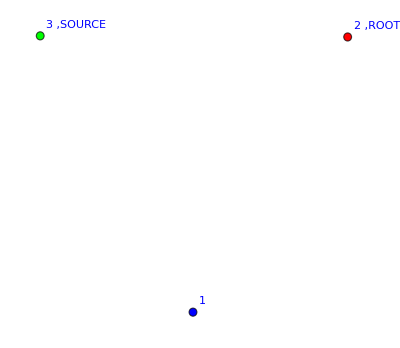

Weight 1

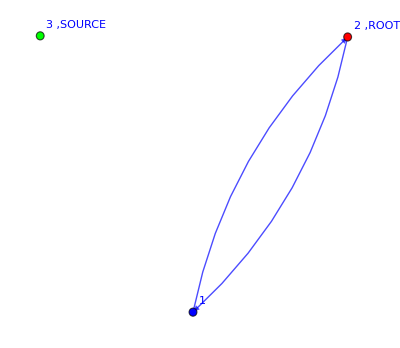

Weight   1
-(-)
  4

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
fields={χ,ϕ,ψ};
endTime=1;
Z=DynamicLERWaction[g,endTime];
ExpectationValue[Z,"fields"->fields,"endTime"->endTime,"print"->False,"draw"->True,"graph"->g]
```

```mathematica
Z//.V[A_]->A;
GeneralizedExpectationValue[%,"draw"->True,"graph"->g]
```

Part::partw: Part 3 of {1,2} does not exist.

Part::partw: Part 3 of {2,1} does not exist.

{-Graphics-,-Graphics-}

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

Two time-slices

```mathematica
endTime=2;
Z=DynamicLERWaction[g,endTime];
Z//.V[A_]->A;
GeneralizedExpectationValue[%]
%/.β[__]->1
```

$Aborted

$Aborted

```mathematica
(*Wich is (Z_t)^2. Correct!!!*)
```

```mathematica
WickContraction[Z,"fields"->fields,"endTime"->endTime]
```

1+V[1+ϕ[1,t_2,0]] V[1+ϕ[2,t_2,0]] V[1+ϕ[3,t_2,0]] V[1+ψ[1,t_2,i_-1]] V[1+ψ[2,t_2,i_-1]] V[1+ψ[3,t_2,i_-1]]+(n R[1,2,RGBColor[0, 0, 1]] R[2,1,RGBColor[0, 0, 1]] β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))+(n R[1,2,RGBColor[0, 0, 1]] R[2,1,RGBColor[0, 0, 1]] V[1+ϕ[1,t_2,0]] V[1+ϕ[2,t_2,0]] V[1+ϕ[3,t_2,0]] V[1+ψ[1,t_2,i_-1]] V[1+ψ[2,t_2,i_-1]] V[1+ψ[3,t_2,i_-1]] β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
(*IT IS WAAAAAY QUICKER!!!!!!!*)
```

```mathematica
ExpectationValue[Z,"fields"->fields,"endTime"->endTime]
```

1+V[1+ϕ[1,t_3,0]] V[1+ϕ[2,t_3,0]] V[1+ϕ[3,t_3,0]] V[1+ψ[1,t_3,i_-1]] V[1+ψ[2,t_3,i_-1]] V[1+ψ[3,t_3,i_-1]]+(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(V[1+ϕ[1,t_3,0]] V[1+ϕ[2,t_3,0]] V[1+ϕ[3,t_3,0]] V[1+ψ[1,t_3,i_-1]] V[1+ψ[2,t_3,i_-1]] V[1+ψ[3,t_3,i_-1]] β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))-(2 V[1+ϕ[1,t_3,0]] V[1+ϕ[2,t_3,0]] V[1+ϕ[3,t_3,0]] V[1+ψ[1,t_3,i_-1]] V[1+ψ[2,t_3,i_-1]] V[1+ψ[3,t_3,i_-1]] β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
%/.V[_]->1
```

2+(2 β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)-(4 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

Now let’s add an external field

With the generalized expectation value

```mathematica
endTime=1;
Z=DynamicLERWaction[g,endTime];
Z//.V[A_]->A;
GeneralizedExpectationValue[%* ϕs[2,Subscript[t, 1],Subscript[i, -1]]]
```

(β[1,3] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
(*Which makes sense since I am not considering any step. endTime=1 means that we consider only one time-slice, i.e. the initial position*)
```

```mathematica
endTime=2;
Z=DynamicLERWaction[g,endTime];
```

```mathematica
(*WARNING: VERY SLOW, DO NOT RUN THIS LINE*)GeneralizedExpectationValue[Z ϕs[2,Subscript[t, 1]]]
```

-(4 β[1,2] β[1,3] β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(4 β[1,3] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
(*The previous line gives*)-(4 β[1,2] β[1,3] β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(4 β[1,3] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))
```

-(4 β[1,2] β[1,3] β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(4 β[1,3] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
%/.β[__]->1
```

3/4

Done with the enhanced WickContraction

###################  Partition Function  ##################

{{},{{1,2,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]}},{{1,2,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]}}}

-Graphics-

-Graphics-

-Graphics-

1+(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

###################  Operator found  ##################

{{{1,3,RGBColor[0, 0, 1]},{1,3,RGBColor[1, 0, 0]},{2,1,RGBColor[1, 0, 0]}}}

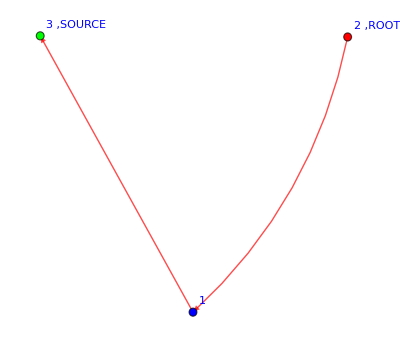

(β[1,3]^2 β[2,1])/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3]))

```mathematica
fields={χ,ϕ,ψ};
endTime=2;
Z=DynamicLERWaction[g,endTime];
ExpectationValue[Z ,"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->True]
Z Op[ϕs[2,Subscript[t, 1],0]];
ExpectationValue[Z Op[ϕs[2,Subscript[t, 1],0]],"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->True]
```

```mathematica
1+V[1+ϕ[1,Subscript[t, 3],0]] V[1+ϕ[2,Subscript[t, 3],0]] V[1+ϕ[3,Subscript[t, 3],0]] V[1+ψ[1,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[2,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[3,Subscript[t, 3],Subscript[i, -1]]]+(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(V[1+ϕ[1,Subscript[t, 3],0]] V[1+ϕ[2,Subscript[t, 3],0]] V[1+ϕ[3,Subscript[t, 3],0]] V[1+ψ[1,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[2,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[3,Subscript[t, 3],Subscript[i, -1]]] β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))-(2 V[1+ϕ[1,Subscript[t, 3],0]] V[1+ϕ[2,Subscript[t, 3],0]] V[1+ϕ[3,Subscript[t, 3],0]] V[1+ψ[1,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[2,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[3,Subscript[t, 3],Subscript[i, -1]]] β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))/.f_[a_,Subscript[t, 3],b_]->f[a,b];
WickContraction[V[1]*%,"fields"->fields,"endTime"->0]
```

###################  Partition Function  ##################

###################  Partition Function  ##################

###################  Partition Function  ##################

2+WickContraction[(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2),print→False,fields→{χ,ϕ,ψ},endTime→0]+WickContraction[-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3])),print→False,fields→{χ,ϕ,ψ},endTime→0]+(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
(*expected*)
```

```mathematica
ϕs[2,Subscript[t, 1],0](β[2,1] ϕ[2,Subscript[t, 1],Subscript[k, 2]] ϕs[1,Subscript[t, 2],Subscript[k, 2]] χs[1,Subscript[t, 1],1] ψs[2,Subscript[t, 2],Subscript[i, -1]])/(β[2,1]+β[2,3])((β[1,3] χ[1,Subscript[t, 1],Subscript[i, 1]] χs[3,Subscript[t, 1],Subscript[i, 1]])/(β[1,2]+β[1,3])χ[3,Subscript[t, 1],1])((β[1,3] ϕ[1,Subscript[t, 2],Subscript[k, 1]] ϕs[3,Subscript[t, 3],Subscript[k, 1]] χs[3,Subscript[t, 2],1] ψs[1,Subscript[t, 3],Subscript[i, -1]])/(β[1,2]+β[1,3])ϕ[3,Subscript[t, 3],0]ψ[1,Subscript[t, 3],Subscript[i, -1]]χ[3,Subscript[t, 2],1])ψ[2,Subscript[t, 2],Subscript[i, -1]]ψs[2,Subscript[t, 3],Subscript[i, -1]]ψ[2,Subscript[t, 3],Subscript[i, -1]]
```

```mathematica
(*Weight*)
```

```mathematica
ϕs[2,Subscript[t, 1],0](β[2,1] ϕ[2,Subscript[t, 1],Subscript[k, 2]] ϕs[1,Subscript[t, 2],Subscript[k, 2]] χs[1,Subscript[t, 1],1] ψs[2,Subscript[t, 2],Subscript[i, -1]])/(β[2,1]+β[2,3])((β[1,3] χ[1,Subscript[t, 1],Subscript[i, 1]] χs[3,Subscript[t, 1],Subscript[i, 1]])/(β[1,2]+β[1,3])χ[3,Subscript[t, 1],1])((β[1,3] ϕ[1,Subscript[t, 2],Subscript[k, 1]] ϕs[3,Subscript[t, 3],Subscript[k, 1]] χs[3,Subscript[t, 2],1] ψs[1,Subscript[t, 3],Subscript[i, -1]])/(β[1,2]+β[1,3])ϕ[3,Subscript[t, 3],0]ψ[1,Subscript[t, 3],Subscript[i, -1]]χ[3,Subscript[t, 2],1])ψ[2,Subscript[t, 2],Subscript[i, -1]]ψs[2,Subscript[t, 3],Subscript[i, -1]]ψ[2,Subscript[t, 3],Subscript[i, -1]]//.f_[_,_,_]->1
```

(β[1,3]^2 β[2,1])/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3]))

```mathematica
(*THEY SEEM TO MATCH!!!!!!!!!*)
```

Regular 2x2 lattice with absorption (i.e. source) at 4

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source][[1]];
g;
fields={χ,ϕ,ψ};
endTime=1;
Z=DynamicLERWaction[g,endTime]
```

V[1+ϕ[1,t_2,0]] V[1+ϕ[2,t_2,0]] V[1+ϕ[3,t_2,0]] V[1+ϕ[4,t_2,0]] V[1+χ[4,t_1,1]] V[1+ψ[1,t_2,j_-1]] V[1+ψ[2,t_2,j_-1]] V[1+ψ[3,t_2,j_-1]] V[1+ψ[4,t_2,j_-1]] V[1+(R[1,2,RGBColor[0, 0, 1]] β[1,2] χ[1,t_1,i_1] χs[2,t_1,i_1])/(β[1,2]+β[1,3])+(R[1,3,RGBColor[0, 0, 1]] β[1,3] χ[1,t_1,i_1] χs[3,t_1,i_1])/(β[1,2]+β[1,3])+(R[1,2,RGBColor[1, 0, 0]] β[1,2] ϕ[1,t_1,k_1] ϕs[2,t_2,k_1] χs[2,t_1,1] ψs[1,t_2,j_-1])/(β[1,2]+β[1,3])+(R[1,3,RGBColor[1, 0, 0]] β[1,3] ϕ[1,t_1,k_1] ϕs[3,t_2,k_1] χs[3,t_1,1] ψs[1,t_2,j_-1])/(β[1,2]+β[1,3])+ψ[1,t_1,j_-1] ψs[1,t_2,j_-1]] V[1+(R[2,1,RGBColor[0, 0, 1]] β[2,1] χ[2,t_1,i_2] χs[1,t_1,i_2])/(β[2,1]+β[2,4])+(R[2,4,RGBColor[0, 0, 1]] β[2,4] χ[2,t_1,i_2] χs[4,t_1,i_2])/(β[2,1]+β[2,4])+(R[2,1,RGBColor[1, 0, 0]] β[2,1] ϕ[2,t_1,k_2] ϕs[1,t_2,k_2] χs[1,t_1,1] ψs[2,t_2,j_-1])/(β[2,1]+β[2,4])+(R[2,4,RGBColor[1, 0, 0]] β[2,4] ϕ[2,t_1,k_2] ϕs[4,t_2,k_2] χs[4,t_1,1] ψs[2,t_2,j_-1])/(β[2,1]+β[2,4])+ψ[2,t_1,j_-1] ψs[2,t_2,j_-1]] V[1+(R[3,1,RGBColor[0, 0, 1]] β[3,1] χ[3,t_1,i_3] χs[1,t_1,i_3])/(β[3,1]+β[3,4])+(R[3,4,RGBColor[0, 0, 1]] β[3,4] χ[3,t_1,i_3] χs[4,t_1,i_3])/(β[3,1]+β[3,4])+(R[3,1,RGBColor[1, 0, 0]] β[3,1] ϕ[3,t_1,k_3] ϕs[1,t_2,k_3] χs[1,t_1,1] ψs[3,t_2,j_-1])/(β[3,1]+β[3,4])+(R[3,4,RGBColor[1, 0, 0]] β[3,4] ϕ[3,t_1,k_3] ϕs[4,t_2,k_3] χs[4,t_1,1] ψs[3,t_2,j_-1])/(β[3,1]+β[3,4])+ψ[3,t_1,j_-1] ψs[3,t_2,j_-1]]

```mathematica
Z/.V[A_]->A/.R[___]->1;
GeneralizedExpectationValue[%]
```

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))-(β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source][[1]];
g;
fields={χ,ϕ,ψ};
endTime=1;
Z=DynamicLERWaction[g,endTime];

ExpectationValue[Z ,"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->False]
```

###################  Partition Function  ##################

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))-(β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))

Two time-slices (it’s very slow, I would need kay’s trick for the vertices AND NOW I HAVE IT!!!!)

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source][[1]];
g;
fields={χ,ϕ,ψ};
endTime=2;
Z=DynamicLERWaction[g,endTime];
ExpectationValue[Z ,"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->False]
```

###################  Partition Function  ##################

1+(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,4])^2)-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))+(β[1,3]^2 β[3,1]^2)/((β[1,2]+β[1,3])^2 (β[3,1]+β[3,4])^2)-(2 β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))+(2 β[1,2] β[1,3] β[2,1] β[3,1])/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,4]) (β[3,1]+β[3,4]))

My favorite graph

Partition function

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]];
```

```mathematica
fields={χ,ϕ,ψ};
endTime=1;
Z=DynamicLERWaction[myFavoriteGraph,endTime];

ExpectationValue[Z ,"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->False]
```

###################  Partition Function  ##################

1-(β[1,2] β[2,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]))-(β[2,3] β[3,2])/((β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]))-(β[1,5] β[5,1])/((β[1,2]+β[1,5]) (β[5,1]+β[5,2]+β[5,4]))-(β[1,2] β[2,5] β[5,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))+(β[1,5] β[2,3] β[3,2] β[5,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]) (β[5,1]+β[5,2]+β[5,4]))-(β[1,5] β[2,1] β[5,2])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))-(β[2,5] β[5,2])/((β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))

With a source at 1:

###################  Operator found  ##################

{{{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{2,3,RGBColor[1, 0, 0]},{3,4,RGBColor[0, 0, 1]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]},{5,2,RGBColor[1, 0, 0]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[1, 0, 0]},{5,4,RGBColor[0, 0, 1]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]},{5,4,RGBColor[1, 0, 0]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[1, 0, 0]},{5,4,RGBColor[0, 0, 1]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]},{5,4,RGBColor[1, 0, 0]}},{{1,5,RGBColor[1, 0, 0]},{5,4,RGBColor[0, 0, 1]},{5,4,RGBColor[1, 0, 0]}},{{1,2,RGBColor[1, 0, 0]},{2,5,RGBColor[0, 0, 1]},{2,5,RGBColor[1, 0, 0]},{5,4,RGBColor[0, 0, 1]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]},{5,4,RGBColor[1, 0, 0]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]},{5,4,RGBColor[1, 0, 0]}},{{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[1, 0, 0]},{2,5,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]}},{{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{2,5,RGBColor[1, 0, 0]},{3,4,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]}}}

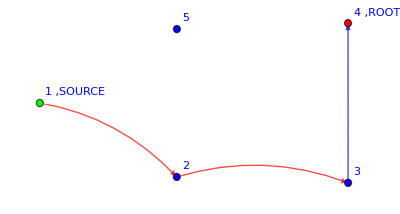

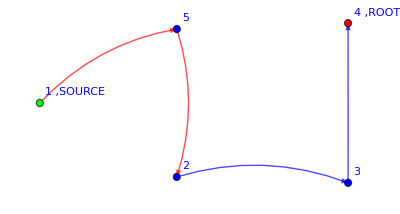

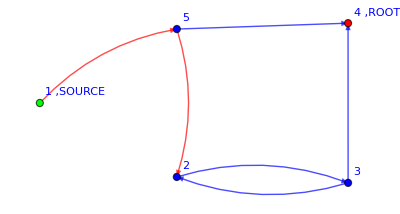

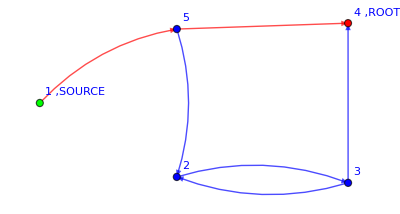

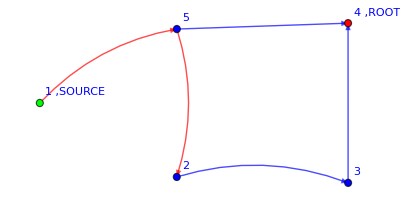

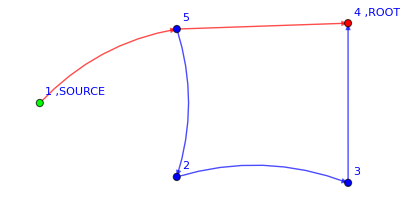

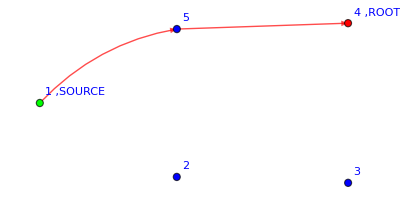

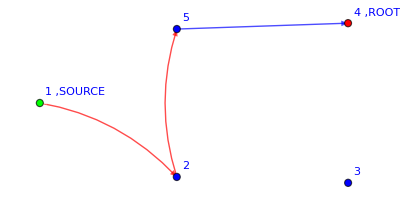

-Graphics-

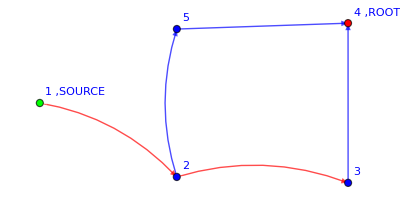

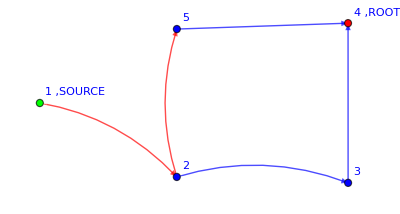

(β[1,2] β[2,3]^2 β[3,4]^2)/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[3,2]+β[3,4])^2)+(β[1,5] β[2,3]^2 β[3,4]^2 β[5,2]^2)/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[3,2]+β[3,4])^2 (β[5,1]+β[5,2]+β[5,4])^2)-(2 β[1,5] β[2,3]^2 β[3,2] β[3,4] β[5,2] β[5,4])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[3,2]+β[3,4])^2 (β[5,1]+β[5,2]+β[5,4])^2)+(2 β[1,5] β[2,3] β[3,4] β[5,2] β[5,4])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]) (β[5,1]+β[5,2]+β[5,4])^2)+(β[1,5] β[5,4]^2)/((β[1,2]+β[1,5]) (β[5,1]+β[5,2]+β[5,4])^2)+(β[1,2] β[2,5]^2 β[5,4]^2)/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[5,1]+β[5,2]+β[5,4])^2)+(β[1,5] β[2,3]^2 β[3,2]^2 β[5,4]^2)/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[3,2]+β[3,4])^2 (β[5,1]+β[5,2]+β[5,4])^2)-(2 β[1,5] β[2,3] β[3,2] β[5,4]^2)/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]) (β[5,1]+β[5,2]+β[5,4])^2)+(2 β[1,2] β[2,3] β[2,5] β[3,4] β[5,4])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[3,2]+β[3,4]) (β[5,1]+β[5,2]+β[5,4]))

```mathematica
g=myFavoriteGraph;
fields={χ,ϕ,ψ};
endTime=2;
Z=DynamicLERWaction[g,endTime];
Z Op[ϕs[1,Subscript[t, 1],0]];
ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->True]
```

## DynamicDLAaction[]

This action should be:

For fields that do not have a color index, we default to set it to j_-1, because in the WickContraction[] it automated with color indices.
Instead, the source is set with index 1, so that it can contract with an external “probe”.

```mathematica
Clear[DynamicDLAaction];
Options[DynamicDLAaction]={"sourceBC"->1,"excludedVertices"->{}};

DynamicDLAaction[graph_,endTime_,OptionsPattern[]]:=Module[{locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j];

locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@graph;

locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[ If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,(*FALSE*)
V[(1+ Sum[locWeights[[x,y]]R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]ϕs[x,Subscript[t, T+1],Subscript[k, x]]χs[y,Subscript[t, T],1]OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1],{y,Length[locVertices]}]+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]+ ϕs[x,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]) ]],{x,Length[locVertices]}]
(*V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])]*);

action=Product[actionTimeSlice[T],{T,endTime}]Product[V[(1+ϕ[x,Subscript[t, endTime+1],Subscript[k, x]])(*This allows the path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, endTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}];

Return[action]

]
```

### Usage example of DynamicDLAaction[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

Partition Function

###################  Partition Function  ##################

{{1},{-1/6,{1,2,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]}},{-1/6,{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]}},{-1/6,{1,5,RGBColor[0, 0, 1]},{5,1,RGBColor[0, 0, 1]}},{-1/18,{1,2,RGBColor[0, 0, 1]},{2,5,RGBColor[0, 0, 1]},{5,1,RGBColor[0, 0, 1]}},{1/36,{1,5,RGBColor[0, 0, 1]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{5,1,RGBColor[0, 0, 1]}},{-1/18,{1,5,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]}},{-1/9,{2,5,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]}}}

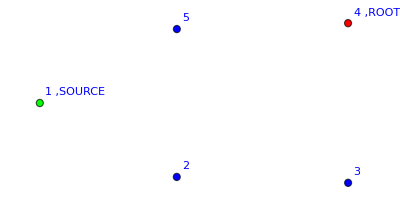

Weight==1

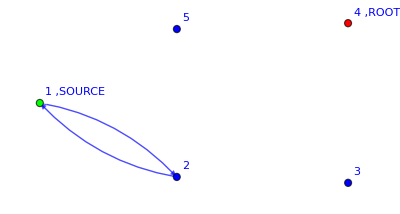

Weight==-1/6

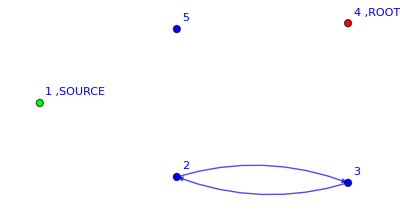

Weight==-1/6

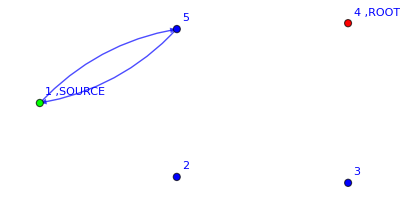

Weight==-1/6

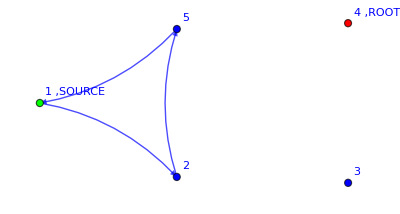

Weight==-1/18

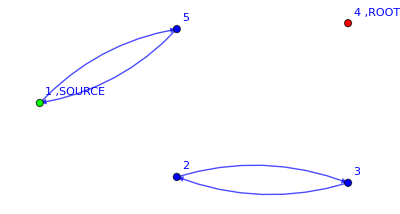

Weight==1/36

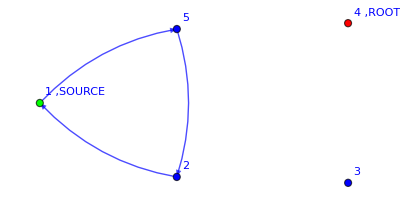

Weight==-1/18

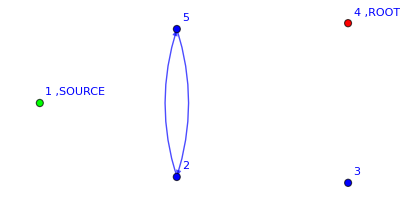

Weight==-1/9

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->True]
```

Observables: Op[ϕs[1,t_1,0]]

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

1-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

Here I would like to compare it to the result obtained by solving the laplace eq but I still need the normalization from the FT

```mathematica
sol=LaplaceEqSolver[g];
phi2=Select[sol,#[[1]]==Φ[2] &][[1,2]];
phi5=Select[sol,#[[1]]==Φ[5] &][[1,2]];
phi2/(phi2+phi5)//FullSimplify
phi5/(phi2+phi5)//FullSimplify
```

(β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4)))/((β_(2,1)+2 β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+2 (β_(5,2)+β_(5,4))))

((β_(2,1)+β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,2)+β_(5,4)))/((β_(2,1)+2 β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+2 (β_(5,2)+β_(5,4))))

Observables: Op[χs[1,t_1,1]], i.e. the solution to the Laplace eq

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[g,endTime];
ExpectationValue[Z  Op[χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

###################  Partition Function  ##################

((R_(1,2,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))))/(1-(R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))))

```mathematica
g=AugmentedGraph[myFavoriteGraph]
Z=DynamicDLAaction[g,endTime];

ExpectationValue[Z  ,"endTime"->endTime,"fields"->fields,"draw"->False]
```

-Graphics-

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))+(β_(1,2) β_(2,1) β_(3,4) β_(4,3))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(3,4) β_(4,3) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,2) β_(2,5) β_(3,4) β_(4,3) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,3) β_(3,4) β_(4,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,1) β_(3,4) β_(4,3) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(3,2) β_(4,3) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,2) β_(2,1) β_(4,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))

Φ evaluated at the new source:

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
(*Which is the same as Z. CORRECT!*)
```

Φ evaluated at the old source			 CORRECT!!!!!

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
ExpectationValue[Z  Op[χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))

###################  Operator found  ##################

(β_(4,6))/(β_(4,3)+β_(4,5)+β_(4,6))-(β_(2,3) β_(3,2) β_(4,6))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(4,6) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
(*Let's check that we get the same result by solving the Laplace equation. First, we need to properly normalize it, i.e. divide by Z*)
```

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
Phi4FT=ExpectationValue[Z  ,"operator"->χs[4,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

###################  Partition Function  ##################

((β_(4,6))/(β_(4,3)+β_(4,5)+β_(4,6))-(β_(2,3) β_(3,2) β_(4,6))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(4,6) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4))))/(1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4))))

```mathematica
(*Now from the Laplace eq*)
```

```mathematica
Phi4Laplace=LaplaceEqSolver[g,"selectSolution"->4]
```

(β_(4,6) (β_(2,1) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4)))/(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,6) β_(5,1)+β_(2,5) β_(3,2) β_(4,6) β_(5,1)+β_(2,1) β_(3,4) β_(4,6) β_(5,1)+β_(2,3) β_(3,4) β_(4,6) β_(5,1)+β_(2,5) β_(3,4) β_(4,6) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,6) β_(5,2)+β_(2,1) β_(3,4) β_(4,6) β_(5,2)+β_(2,3) β_(3,4) β_(4,6) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4)+β_(2,1) β_(3,2) β_(4,6) β_(5,4)+β_(2,5) β_(3,2) β_(4,6) β_(5,4)+β_(2,1) β_(3,4) β_(4,6) β_(5,4)+β_(2,3) β_(3,4) β_(4,6) β_(5,4)+β_(2,5) β_(3,4) β_(4,6) β_(5,4))

```mathematica
(*And now, let's subtract them*)
```

```mathematica
Phi4Laplace-Phi4FT//FullSimplify
```

0

```mathematica
(*CORRECT!!!!!!!!*)
```

### Let’s check that kay’s trick for the total current works: IT WORKS ONLY FOR SYMMETRICAL β BUT WITH ANY σ!!!!!!

```mathematica
g=AugmentedGraph[myFavoriteGraph];
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
Limit[σ(ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ),σ->∞]
```

###################  Operator found  ##################

(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4))/(β_(2,1) β_(3,2) β_(5,1)+β_(2,3) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,3) β_(3,2) β_(5,2)+β_(2,5) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,5) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,3) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4))

```mathematica
Z2=DynamicDLAaction[myFavoriteGraph,endTime,"excludedVertices"->{1}];
ExpectationValue[Z2  Op[χs[2,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]+
ExpectationValue[Z2  Op[χs[5,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]-

ExpectationValue[Z2  Op[χs[2,Subscript[t, 1],1]+χs[5,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

###################  Operator found  ##################

###################  Operator found  ##################

0

```mathematica
(*Ok, I can insert the operators directly inside Op[]*)
```

Kay’s trick works only with symmetrical weights!!!!!

```mathematica
(*Now let's verify that kay's trick works*)
```

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
Limit[σ*(ExpectationValue[Z  ,"operator"->(χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ),σ->∞]

Z2=DynamicDLAaction[myFavoriteGraph,endTime,"excludedVertices"->{1}];
ExpectationValue[Z2,"operator"-> (β[1,2]χs[2,Subscript[t, 1],1]+β[1,5]χs[5,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False]
%%%-%//FullSimplify
%//.β[a_,b_]/;(a<b):>β[b,a]//FullSimplify
```

###################  Operator found  ##################

###################  Partition Function  ##################

(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4))/(β_(2,1) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4))

###################  Operator found  ##################

###################  Partition Function  ##################

((β_(1,2) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(5,4))/(β_(5,1)+β_(5,2)+β_(5,4))+(β_(1,2) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))))/(1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))))

(β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)-β_(1,5) β_(2,3) β_(3,4) β_(5,2)-β_(1,5) (β_(2,5) β_(3,2)+(β_(2,3)+β_(2,5)) β_(3,4)) β_(5,4)+β_(2,1) ((β_(3,2) β_(4,3)+(β_(3,2)+β_(3,4)) β_(4,5)) (β_(5,1)+β_(5,2))-(β_(1,5) (β_(3,2)+β_(3,4))-β_(3,2) β_(4,3)) β_(5,4))+β_(1,2) (-β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)-β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4))))/(β_(2,5) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,4))+β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4))+β_(2,1) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

0

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
Limit[σ*(ExpectationValue[Z Op[(χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1])],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ),σ->∞]

Z2=DynamicDLAaction[myFavoriteGraph,endTime,"excludedVertices"->{1}];
ExpectationValue[Z2 Op[(β[1,2]χs[2,Subscript[t, 1],1]+β[1,5]χs[5,Subscript[t, 1],1])],"endTime"->endTime,"fields"->fields,"draw"->False]
%%%-%//FullSimplify
%//.β[a_,b_]/;(a<b):>β[b,a]//FullSimplify
```

###################  Operator found  ##################

(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4))/(β_(2,1) β_(3,2) β_(5,1)+β_(2,3) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,3) β_(3,2) β_(5,2)+β_(2,5) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,5) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,3) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4))

###################  Operator found  ##################

(β_(1,2) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(5,4))/(β_(5,1)+β_(5,2)+β_(5,4))+(β_(1,2) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

(β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)-β_(1,5) β_(2,3) β_(3,4) β_(5,2)-β_(1,5) (β_(2,5) β_(3,2)+(β_(2,3)+β_(2,5)) β_(3,4)) β_(5,4)+β_(2,1) ((β_(3,2) β_(4,3)+(β_(3,2)+β_(3,4)) β_(4,5)) (β_(5,1)+β_(5,2))-(β_(1,5) (β_(3,2)+β_(3,4))-β_(3,2) β_(4,3)) β_(5,4))+β_(1,2) (-β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)-β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4))))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

0

Does it work for any σ? YESSS

```mathematica
g
```

-Graphics-

Exclude just 1: CORRECT!!!!

```mathematica
AugmGraph=AugmentedGraph[myFavoriteGraph];
g=AugmGraph[[1]];
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
exp1=(ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ)
exp2=(ExpectationValue[Z  Op[χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ)
```

###################  Operator found  ##################

1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

###################  Operator found  ##################

σ/(σ+β_(4,3)+β_(4,5))-(σ β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))-(σ β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
exp2/.σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5])*A_+σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5])*B_+σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5])->HoldForm[σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5])*(A+B+1)]
```

(σ (-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+1))/(σ+β_(4,3)+β_(4,5))

```mathematica
σ (exp1-exp2)
```

σ (1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-σ/(σ+β_(4,3)+β_(4,5))+(σ β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(σ β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4))))

```mathematica
Limit[σ (exp1-exp2), σ -> ∞]-((-(Subscript[β, 3,4] Subscript[β, 4,3])/((Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]))+(Subscript[β, 2,5] Subscript[β, 3,4] Subscript[β, 4,3] Subscript[β, 5,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))-(Subscript[β, 2,3] Subscript[β, 3,4] Subscript[β, 4,5] Subscript[β, 5,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))-(Subscript[β, 2,5] Subscript[β, 3,2] Subscript[β, 4,3] Subscript[β, 5,4])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))-(Subscript[β, 4,5] Subscript[β, 5,4])/((σ+Subscript[β, 4,3]+Subscript[β, 4,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))+(Subscript[β, 2,3] Subscript[β, 3,2] Subscript[β, 4,5] Subscript[β, 5,4])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4])))(σ+Subscript[β, 4,3]+Subscript[β, 4,5])+exp2(σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5]))^-1(Subscript[β, 4,3]+Subscript[β, 4,5]))//FullSimplify
```

0

```mathematica
(*CORRECT!!! THE LIMIT σ->∞ IS THE SAME AS THE BIG PARENTHESES. CHECK ONENOTE NOTEBOOK FOR DETAILS*)
```

```mathematica
Limit[σ(1-σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5])),σ->∞]
```

β_(4,3)+β_(4,5)

```mathematica
Limit[σ((Subscript[β, 3,4] Subscript[β, 4,3])/((Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]))),σ->∞]
```

(β_(3,4) β_(4,3))/(β_(3,2)+β_(3,4))

```mathematica
exp3=ExpectationValue[Z Op[β[1,2]χs[2,Subscript[t, 1],1]+β[1,5]χs[5,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ
```

###################  Operator found  ##################

(σ β_(1,2) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))+(σ β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(σ β_(1,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(σ β_(1,2) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(σ β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
σ(exp1-exp2)-exp3//FullSimplify
%//.β[a_,b_]/;(a<b):>β[b,a]//FullSimplify
```

(σ (β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)-β_(1,5) β_(2,3) β_(3,4) β_(5,2)-β_(1,5) (β_(2,5) β_(3,2)+(β_(2,3)+β_(2,5)) β_(3,4)) β_(5,4)+β_(2,1) ((β_(3,2) β_(4,3)+(β_(3,2)+β_(3,4)) β_(4,5)) (β_(5,1)+β_(5,2))-(β_(1,5) (β_(3,2)+β_(3,4))-β_(3,2) β_(4,3)) β_(5,4))+β_(1,2) (-β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)-β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4)))))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

0

Exclude 1 and 2: CORRECT!!!!

```mathematica
AugmGraph=AugmentedGraph[myFavoriteGraph];
g=AugmGraph[[1]];
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1,2}];
exp1=σ(ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ)
```

###################  Operator found  ##################

σ (1-σ/(σ+β_(4,3)+β_(4,5))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))-(β_(4,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4))))

```mathematica
exp2=ExpectationValue[Z Op[β[2,3]χs[3,Subscript[t, 1],1]+(β[1,5]+β[2,5])χs[5,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ
```

###################  Operator found  ##################

(σ β_(2,3) β_(3,4))/((β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))+(σ β_(1,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(σ β_(2,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
exp1-exp2//FullSimplify
%//.β[a_,b_]/;(a<b):>β[b,a]//FullSimplify
```

-(σ (β_(3,4) (β_(2,3)-β_(4,5))-β_(3,2) (β_(4,3)+β_(4,5))) (β_(5,1)+β_(5,2))+σ (β_(2,3) β_(3,4)+β_(1,5) (β_(3,2)+β_(3,4))+β_(2,5) (β_(3,2)+β_(3,4))-β_(3,2) β_(4,3)) β_(5,4))/((β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

0

### β or β/r? Answer: β!!

We want to check whether we need to use β or β/r in the DLA dynamical action

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
g=AugmentedGraph[myFavoriteGraph];
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
DLAnorm=Limit[σ(ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ),σ->∞]
```

###################  Operator found  ##################

(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4))/(β_(2,1) β_(3,2) β_(5,1)+β_(2,3) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,3) β_(3,2) β_(5,2)+β_(2,5) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,5) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,3) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4))

```mathematica
g=myFavoriteGraph;
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];
exp=ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]/DLAnorm/.β[__]->1
ExtractPaths[exp](*This is nicely normalized!!!*)
```

###################  Operator found  ##################

18/11 (1-1/6 R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1])+1/6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1])-1/9 R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])+1/18 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])+1/3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])+1/9 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1])-1/18 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]))

{{18/11},{-3/11,{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]}},{3/11,{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]}},{-2/11,{2,5,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]}},{1/11,{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]}},{6/11,{1,5,RGBColor[1, 0, 0]},{5,4,RGBColor[0, 0, 1]}},{2/11,{1,2,RGBColor[1, 0, 0]},{2,5,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]}},{-1/11,{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]}}}

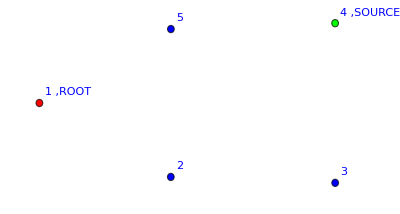

Weight==18/11

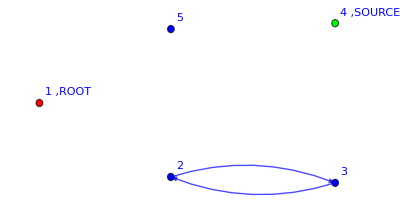

Weight==-3/11

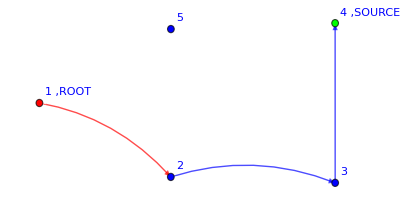

Weight==3/11

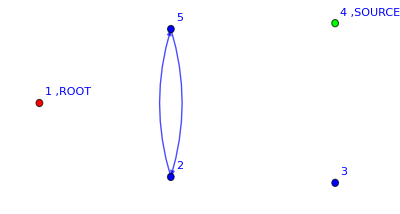

Weight==-2/11

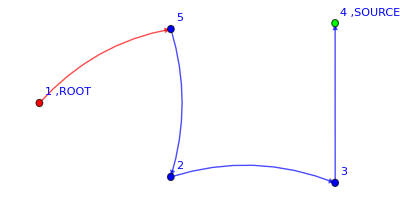

Weight==1/11

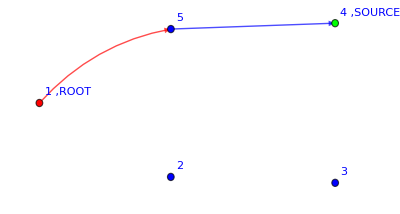

Weight==6/11

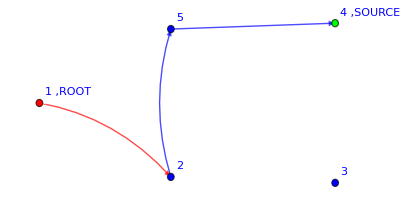

Weight==2/11

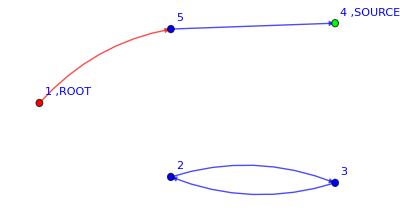

Weight==-1/11

```mathematica
DrawFromExpression[exp];
```

Now, if we use β/r: NOT PROPERLY NORMALIZED

```mathematica
g=AugmentedGraph[myFavoriteGraph];
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
DLAnorm=Limit[σ(ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ),σ->∞]
```

###################  Operator found  ##################

(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4))/(β_(2,1) β_(3,2) β_(5,1)+β_(2,3) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,3) β_(3,2) β_(5,2)+β_(2,5) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,5) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,3) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4))

```mathematica
g=myFavoriteGraph;
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];
exp=ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]/DLAnorm/.β[__]->1
ExtractPaths[exp]
```

###################  Operator found  ##################

18/11 (1-1/6 R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1])+1/12 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1])-1/9 R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])+1/36 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])+1/6 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])+1/18 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1])-1/36 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]))

{{(5 R_(1,2,RGBColor[1, 0, 0]))/22},{(3 R_(1,5,RGBColor[1, 0, 0]))/11}}

```mathematica
(*Not properly normalized!!!*)
```

### Can I send each field to zero immediately or do I need to do it at the end? Answer: YESSS!

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

Partition Function right away

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

Partition function field by field

```mathematica
fields={ϕ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
fields={χ};
ExpectationValue[%%,"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

V[1+χ_(4,1)] V[1+(β_(3,2) χ_(3,i_3) (χ^*)_(2,i_3))/(β_(3,2)+β_(3,4))+(β_(3,4) χ_(3,i_3) (χ^*)_(4,i_3))/(β_(3,2)+β_(3,4))] V[1+(β_(5,1) χ_(5,i_5) (χ^*)_(1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(β_(5,2) χ_(5,i_5) (χ^*)_(2,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(β_(5,4) χ_(5,i_5) (χ^*)_(4,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))] V[1+(β_(1,2) χ_(1,i_1) (χ^*)_(2,i_1))/(β_(1,2)+β_(1,5))+(β_(1,5) χ_(1,i_1) (χ^*)_(5,i_1))/(β_(1,2)+β_(1,5))] V[1+(β_(2,1) χ_(2,i_2) (χ^*)_(1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(β_(2,3) χ_(2,i_2) (χ^*)_(3,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(β_(2,5) χ_(2,i_2) (χ^*)_(5,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))]

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
(*Ok, for the partition funciton it works. But in the partition function only χ is used*)
```

Observables: Op[ϕs[1,t_1,0]]

Right away

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]
```

###################  Operator found  ##################

1-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

Field by field

```mathematica
fields={ϕ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]
fields={χ};
ExpectationValue[%%,"endTime"->endTime,"fields"->fields,"draw"->False"Rrule"->{}]
```

###################  Operator found  ##################

V[1+χ_(4,1)] V[1+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) χ_(3,i_3) (χ^*)_(2,i_3))/(β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) χ_(3,i_3) (χ^*)_(4,i_3))/(β_(3,2)+β_(3,4))] V[1+(R_(5,1,RGBColor[0, 0, 1]) β_(5,1) χ_(5,i_5) (χ^*)_(1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,2,RGBColor[0, 0, 1]) β_(5,2) χ_(5,i_5) (χ^*)_(2,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,4,RGBColor[0, 0, 1]) β_(5,4) χ_(5,i_5) (χ^*)_(4,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))] V[1+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) χ_(2,i_2) (χ^*)_(1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) χ_(2,i_2) (χ^*)_(3,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,5,RGBColor[0, 0, 1]) β_(2,5) χ_(2,i_2) (χ^*)_(5,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))]+R_(1,2,RGBColor[1, 0, 0]) V[1+χ_(4,1)] V[1+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) χ_(3,i_3) (χ^*)_(2,i_3))/(β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) χ_(3,i_3) (χ^*)_(4,i_3))/(β_(3,2)+β_(3,4))] V[1+(R_(5,1,RGBColor[0, 0, 1]) β_(5,1) χ_(5,i_5) (χ^*)_(1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,2,RGBColor[0, 0, 1]) β_(5,2) χ_(5,i_5) (χ^*)_(2,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,4,RGBColor[0, 0, 1]) β_(5,4) χ_(5,i_5) (χ^*)_(4,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))] V[1+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) χ_(2,i_2) (χ^*)_(1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) χ_(2,i_2) (χ^*)_(3,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,5,RGBColor[0, 0, 1]) β_(2,5) χ_(2,i_2) (χ^*)_(5,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))] β_(1,2) (χ^*)_(2,1)+R_(1,5,RGBColor[1, 0, 0]) V[1+χ_(4,1)] V[1+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) χ_(3,i_3) (χ^*)_(2,i_3))/(β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) χ_(3,i_3) (χ^*)_(4,i_3))/(β_(3,2)+β_(3,4))] V[1+(R_(5,1,RGBColor[0, 0, 1]) β_(5,1) χ_(5,i_5) (χ^*)_(1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,2,RGBColor[0, 0, 1]) β_(5,2) χ_(5,i_5) (χ^*)_(2,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,4,RGBColor[0, 0, 1]) β_(5,4) χ_(5,i_5) (χ^*)_(4,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))] V[1+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) χ_(2,i_2) (χ^*)_(1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) χ_(2,i_2) (χ^*)_(3,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,5,RGBColor[0, 0, 1]) β_(2,5) χ_(2,i_2) (χ^*)_(5,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))] β_(1,5) (χ^*)_(5,1)

###################  Partition Function  ##################

###################  Partition Function  ##################

###################  Partition Function  ##################

1-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
(*OK!! IT SEEMS THAT I CAN DO FIRST A FIELD, SET TO ZERO, THEN THE OTHERS*)
```

## ModWickContraction[]

```mathematica
Clear[ModWickContraction];
Options[ModWickContraction]={"print"->False,"fields"->{χ}, "endTime"->0(*It is set to 0 for the statical case*),"replicas"->0};

ModWickContraction[A_ +B_,OptionsPattern[]]:=ModWickContraction[A,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"]]+ModWickContraction[B,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"]];

ModWickContraction[A_ +B__+C__,OptionsPattern[]]:=ModWickContraction[A,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"]]+ModWickContraction[B+C,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"]];

ModWickContraction[A_?NumericQ,OptionsPattern[]]:=A;


(*ModWickContraction[Op[A_] *B_, OptionsPattern[]]:=
ModWickContraction[Op[A_]^nn_ *B_, OptionsPattern[]]*)

(*################################################################################
									Expectation values                            
##############################################################################*)
(*There are two possible contributions for each field: 1) it is not contracted: χ->0; 2) it is contracted*)

ModWickContraction[Op[A_] *B_, OptionsPattern[]]:=Module[{locFields={}, starFields={}, deltaFields={},deltaStarFields={},contributions=0,z,zTemp,κ,j,l,r,timeIndex,replicaIndex},
z=Op[A]B;

Print["################### Operators found  ##################"];


locFields=OptionValue["fields"];

For[l=1,l<=Length[locFields],l++,
AppendTo[starFields, ToExpression[ToString[locFields[[l]]] <> "s"]];
AppendTo[deltaFields, ToExpression["δ"<>ToString[locFields[[l]]] ]];
AppendTo[deltaStarFields,ToExpression["δ"<> ToString[starFields[[l]]] ]];
];(*End of loop to define the fields*)

If[OptionValue["print"],
Print[locFields,starFields,deltaFields,deltaStarFields];
];

(*Start a loop over time*)
For[timeIndex=0,timeIndex<=(OptionValue["endTime"]),timeIndex++,

If[OptionValue["print"],
Print["###################  Time "<> ToString[timeIndex+1]<>"  ##################"];
Print[z]
];

If[OptionValue["endTime"]!=0,
(*TRUE*)z=z//.f_[x_,Subscript[t, (timeIndex+1)],a__]->f[x,a]
];


(*Start a loop over "replicas"*)
For[replicaIndex=0,replicaIndex<=(OptionValue["replicas"]),replicaIndex++,

If[replicaIndex==0, 
(*TRUE*)If[OptionValue["replicas"]==0,1,Continue[]],
(*FALSE*)z=z//.f_[x_,a_,Subscript[m, (replicaIndex)]]->f[x,a];
];


(*Start a loop over fields*)
For[l=1,l<=Length[locFields],l++,

(*Start a loop over space*)
For[j=1,j<=100,j++,

(*First contribution*)
zTemp=z//.locFields[[l]][j,a_]->0//.starFields[[l]][j,a_]->0;
If[zTemp-z=!=0,
contributions=zTemp;
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": First contribution ####"];
Print[contributions]]
];

For[r=1,r<=1,r++,
(*Second contribution*)

zTemp=z/. locFields[[l]][j,a_]->locFields[[l]][j,a]+κ *deltaFields[[l]][j,a];
If[zTemp-z=!=0,
z=Factorial[r]^-1*D[zTemp,{κ,r}]/.κ->0;
];

zTemp=z/. starFields[[l]][j,a_]->starFields[[l]][j,a]+κ *deltaStarFields[[l]][j,a];
If[zTemp-z=!=0,
z=Factorial[r]^-1*D[zTemp,{κ,r}]/.κ->0;
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": second contribution ####"];
Print[z]
]
];

z=Expand[z];
zTemp=z//.deltaFields[[l]][j,a_]*deltaStarFields[[l]][j,b_](*/;(!NumericQ[a*b]):>*)->δ[a,b];

If[zTemp-z=!=0,
If[OptionValue["print"],
Print["#### Contraction "<>ToString[j]<>" ####"];
Print[z=zTemp]
]
];
z=zTemp/.deltaFields[[l]][j,a_]->0/.deltaStarFields[[l]][j,b_]->0;


If[contributions-z=!=0,
contributions+=z;
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": total contribution ####"];
Print[contributions]]
];

z=contributions;
contributions=0;

];(*End of loop over gaussian orders*)
];(*End of loop over space*)

z=z/.locFields[[l]][x_,a_]->0;
z=z/.starFields[[l]][x_,a_]->0;

];(*End of loop over fields*)
(*
For[l=1,l<=Length[locFields],l++,
z=z/.locFields[[l]][x_,a_]->0;
z=z/.starFields[[l]][x_,a_]->0;
];*)

z=z//.Σδrule;
contributions=0;
];(*End of loop over replicas*)
];(*End of loop over time*)

Return[z]
];


(*ModWickContraction[Op[A_]^nn_ *B_, OptionsPattern[]]:=Module[{locFields={}, starFields={}, deltaFields={},deltaStarFields={},contributions=0,z,zTemp,κ,j,l,r,timeIndex},
z=Op[A]^nn B;

Print["###################  Operator found  ##################"];


locFields=OptionValue["fields"];

For[l=1,l<=Length[locFields],l++,
AppendTo[starFields, ToExpression[ToString[locFields[[l]]] <> "s"]];
AppendTo[deltaFields, ToExpression["δ"<>ToString[locFields[[l]]] ]];
AppendTo[deltaStarFields,ToExpression["δ"<> ToString[starFields[[l]]] ]];
];(*End of loop to define the fields*)

If[OptionValue["print"],
Print[locFields,starFields,deltaFields,deltaStarFields];
];

For[timeIndex=0,timeIndex<=(OptionValue["endTime"]),timeIndex++,

(*
If[timeIndex==0, 
(*TRUE*)If[OptionValue["endTime"]==0,timeIndex++,Continue[]],
(*FALSE*)z=z//.f_[x_,Subscript[t, timeIndex],a_]->f[x,a];
];*)

If[OptionValue["print"],
Print["###################  Time "<> ToString[timeIndex+1]<>"  ##################"];
Print[z]
];

If[OptionValue["endTime"]!=0,
(*TRUE*)z=z//.f_[x_,Subscript[t, (timeIndex+1)],a_]->f[x,a]
];

For[j=1,j<=100,j++,
For[l=1,l<=Length[locFields],l++,
(*First contribution*)
zTemp=z//.locFields[[l]][j,a_]->0//.starFields[[l]][j,a_]->0;
If[zTemp-z=!=0,
contributions=zTemp;
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": First contribution ####"];
Print[contributions]]
];

For[r=1,r<=nn,r++,
(*Second contribution*)

zTemp=z/. locFields[[l]][j,a_]->locFields[[l]][j,a]+κ *deltaFields[[l]][j,a];
If[zTemp-z=!=0,
z=Factorial[r]^-1*D[zTemp,{κ,r}]/.κ->0;
];

zTemp=z/. starFields[[l]][j,a_]->starFields[[l]][j,a]+κ *deltaStarFields[[l]][j,a];
If[zTemp-z=!=0,
z=Factorial[r]^-1*D[zTemp,{κ,r}]/.κ->0;
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": second contribution ####"];
Print[z]
]
];

z=Expand[z];
zTemp=z//.deltaFields[[l]][j,a_]*deltaStarFields[[l]][j,b_](*/;(!NumericQ[a*b]):>*)->δ[a,b];

If[zTemp-z=!=0,
If[OptionValue["print"],
Print["#### Contraction "<>ToString[j]<>" ####"];
Print[z=zTemp]
]
];
z=zTemp/.deltaFields[[l]][j,a_]->0/.deltaStarFields[[l]][j,b_]->0;


If[contributions-z=!=0,
contributions+=z;
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": total contribution ####"];
Print[contributions]]
];

z=contributions;
contributions=0;

];(*End of loop over gaussian orders*)
];(*End of loop over fields*)
];(*End of loop over space*)

For[l=1,l<=Length[locFields],l++,
z=z/.locFields[[l]][x_,a_]->0;
z=z/.starFields[[l]][x_,a_]->0;
];

z=z//.Σδrule;
];(*End of loop over time*)

Return[z]
];*)


(*################################################################################
									Partition Function                             
##############################################################################*)
(*There are two possible contributions for each field: 1) it is not contracted: χ->0; 2) it is contracted*)

ModWickContraction[V[A_] *B_, OptionsPattern[]]:=Module[{locFields={}, starFields={}, deltaFields={},deltaStarFields={},contributions=0,z,zTemp,κ,j,l,timeIndex},
z=V[A]B;

Print["###################  Partition Function  ##################"];


locFields=OptionValue["fields"];

For[l=1,l<=Length[locFields],l++,
AppendTo[starFields, ToExpression[ToString[locFields[[l]]] <> "s"]];
AppendTo[deltaFields, ToExpression["δ"<>ToString[locFields[[l]]] ]];
AppendTo[deltaStarFields,ToExpression["δ"<> ToString[starFields[[l]]] ]]
];(*End of loop to define the fields*)

If[OptionValue["print"],
Print[locFields,starFields,deltaFields,deltaStarFields]
];

For[timeIndex=0,timeIndex<=(OptionValue["endTime"]),timeIndex++,

(*If[timeIndex==0, 
(*TRUE*)If[OptionValue["endTime"]==0,timeIndex++,Continue[]],
(*FALSE*)z=z//.f_[x_,Subscript[t, timeIndex],a_]->f[x,a];
];*)

If[OptionValue["print"],
Print["###################  Time "<> ToString[timeIndex+1]<>"  ##################"];
Print["Z before"];
Print[z]
];

If[OptionValue["endTime"]!=0,
(*TRUE*)z=z//.f_[x_,Subscript[t, (timeIndex+1)],a_]->f[x,a]
];

If[OptionValue["print"],
Print["Z After"];
Print[z]
];

(*Start a loop over fields*)
For[l=1,l<=Length[locFields],l++,

(*Start a loop over space*)
For[j=1,j<=100,j++,

(*First contribution*)
zTemp=z//.locFields[[l]][j,a_]->0//.starFields[[l]][j,a_]->0;
If[zTemp-z=!=0,
contributions=zTemp;
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": First contribution ####"];
Print[contributions]]
];

(*Second contribution*)
zTemp=z/. locFields[[l]][j,a_]->locFields[[l]][j,a]+κ *deltaFields[[l]][j,a];
If[zTemp-z=!=0,
z=D[zTemp,κ]/.κ->0;
];

zTemp=z/. starFields[[l]][j,a_]->starFields[[l]][j,a]+κ *deltaStarFields[[l]][j,a];
If[zTemp-z=!=0,
z=D[zTemp,κ]/.κ->0;
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": second contribution ####"];
Print[z]
]
];

z=Expand[z];
zTemp=z//.deltaFields[[l]][j,a_]*deltaStarFields[[l]][j,b_](*/;(!NumericQ[a*b]):>*)->δ[a,b];

If[zTemp-z=!=0,
If[OptionValue["print"],
Print["#### Contraction "<>ToString[j]<>" ####"];
Print[z=zTemp]
]
];

z=zTemp/.deltaFields[[l]][j,a_]->0/.deltaStarFields[[l]][j,b_]->0;


If[contributions-z=!=0,
contributions+=z;
If[OptionValue["print"],
Print["#### "<>ToString[j]<>": total contribution ####"];
Print[contributions]]
];

z=contributions;
contributions=0;

];(*End of loop over space*)

z=z/.locFields[[l]][x_,a_]->0;
z=z/.starFields[[l]][x_,a_]->0;

];(*End of loop over fields*)

(*
For[l=1,l<=Length[locFields],l++,
z=z/.locFields[[l]][x_,a_]->0;
z=z/.starFields[[l]][x_,a_]->0
];*)

z=z//.Σδrule;

];(*End of loop over time*)

Return[z]
];
```

## ModExpectationValue[]

WARNING: works only with augmented graphs!!!! g=AugmentedGraph[...]

```mathematica
Clear[ModExpectationValue];
Options[ModExpectationValue]={"operator"->1,"print"->False, "fields"->{χ},"endTime"->1,"replicas"->0,"draw"->False,"graph"->graph[[1]],"oldSource"->graph[[2]],"newSource"->graph[[3]],  "Rrule"->{R[__]->1}, "σLimit"->σ};

ModExpectationValue[Z_,OptionsPattern[]]:=Module[{z,terms,graphs={},i},
Clear[σ,n];

If[OptionValue["operator"]===1,
(*True*)z=ModWickContraction[Z,
"print"->OptionValue["print"], 
"fields"->OptionValue["fields"],
"endTime"->OptionValue["endTime"],
"replicas"->OptionValue["replicas"]
],
(*False*)z=ModWickContraction[Z*Op[OptionValue["operator"]],
"print"->OptionValue["print"], 
"fields"->OptionValue["fields"],
"endTime"->OptionValue["endTime"],
"replicas"->OptionValue["replicas"]
]/ModWickContraction[Z, "fields"->OptionValue["fields"],"endTime"->OptionValue["endTime"],"replicas"->OptionValue["replicas"]]
];

z=z//.δruleExternal;
z=z/.n->-1;

If[OptionValue["draw"],
(*True*)
z=z//.R[a_,b_,c_]^n_->R[a,b,c];
terms=List @@ (z+Zeta[3]);
terms=terms//.β[__]->1;
terms=DeleteElements[terms,{Zeta[3]}];
terms=Outer[List,terms];
terms=terms//.Times->List;
terms=monoFlatten@@@terms;
terms=terms//.R[a_,b_,c_]->{a,b,c};
(*For[i=1,i<=Length[terms],i++,
terms[[i]]=DeleteElements[terms[[i]],{a_?NumericQ}];
];*)
Print[terms];
z=z/.R[___]->1;

For[i=1,i<=Length[terms],i++,
AppendTo[graphs,DrawOnGraph[OptionValue["graph"],terms[[i,2;;]],"drawOthers"->False]];
Print[graphs[[i]]];
Print[Weight ==terms[[i,1]]];
];,

(*False*)z=z/.OptionValue["Rrule"]];

z=z/.β[OptionValue["oldSource"], OptionValue["newSource"]]->σ;

(*If[OptionValue["σLimit"]!=σ,*)
z=Limit[z,σ->OptionValue["σLimit"]];

Return[z]
]
```

## ModDynamicDLAaction[]

Without ξ

```mathematica
Clear[ModDynamicDLAaction];
Options[ModDynamicDLAaction]={"sourceBC"->1,"excludedVertices"->{},"replicas"->1};

ModDynamicDLAaction[graph_,endTime_,oldSource_,OptionsPattern[]]:=Module[{locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,σ,m,M];
M=OptionValue["replicas"];

locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@graph;

locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[ If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,(*FALSE*)
V[(1+ Sum[locWeights[[x,y]]R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, x]]ϕs[x,Subscript[t, T+1],Subscript[k, x]]χs[y,Subscript[t, T],Subscript[1, 0]]
Product[ ψs[x,Subscript[t, T],Subscript[j, x],Subscript[m, mm]],{mm,M}]ϕ[x,Subscript[t, T],Subscript[k, x]],{y,Length[locVertices]}]+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x,0]]χ[x,Subscript[t, T],Subscript[i, x,0]],{y,Length[locVertices]}]+ ϕs[x,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]) ]
Product[ V[1+ψs[x,Subscript[t, T+1],Subscript[j, x],Subscript[m, mm]]ψ[x,Subscript[t, T],Subscript[j, x],Subscript[m, mm]]+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Yellow]χs[y,Subscript[t, T],Subscript[i, x],Subscript[m, mm]]χ[x,Subscript[t, T],Subscript[i, x],Subscript[m, mm]],{y,Length[locVertices]}](*This allows to avoid the path while constructing the loops*)],{mm,M}]] ,{x,Length[locVertices]}] 
Product[ Op[σ(χs[locSource,Subscript[t, T],1,Subscript[m, mm]]-χs[oldSource,Subscript[t, T],1,Subscript[m, mm]])χ[locSource,Subscript[t, T],1,Subscript[m, mm]](*This allows to compute the Denominator*)],{mm,M}]
V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],Subscript[1, 0]])(*This allows to compute the solution to the Laplace eq*)];

action=Product[actionTimeSlice[T],{T,endTime}]Product[V[(1+ϕ[x,Subscript[t, endTime+1],Subscript[k, x]])(*This allows the path tracker to be absorbed at the end*) ]
Product[ V[(1+ψ[x,Subscript[t, endTime+1],Subscript[j, x],Subscript[m, mm]])(*This allows the AUXILIARY path tracker to be absorbed at the end*) ],{mm,M}]
V[(1+ϕ[x,Subscript[t, endTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}];

Return[action]

]
```

EXTRA ξ field

```mathematica
Clear[ModDynamicDLAaction];
Options[ModDynamicDLAaction]={"sourceBC"->1,"excludedVertices"->{},"replicas"->1};

ModDynamicDLAaction[graph_,endTime_,oldSource_,OptionsPattern[]]:=Module[{locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,σ,m,M];
M=OptionValue["replicas"];

locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@graph;

locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[ If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,(*FALSE*)
V[(1+ Sum[locWeights[[x,y]]R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, x]]ϕs[x,Subscript[t, T+1],Subscript[k, x]]χs[y,Subscript[t, T],Subscript[1, 0]]OptionValue["sourceBC"] χ[locSource,Subscript[t, T],Subscript[1, 0]]
Product[ ψs[x,Subscript[t, T],Subscript[j, x],Subscript[m, mm]],{mm,M}]ϕ[x,Subscript[t, T],Subscript[k, x]],{y,Length[locVertices]}]+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x,0]]χ[x,Subscript[t, T],Subscript[i, x,0]],{y,Length[locVertices]}]+ ϕs[x,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]) ]
Product[ V[1+ψs[x,Subscript[t, T+1],Subscript[j, x],Subscript[m, mm]]ψ[x,Subscript[t, T],Subscript[j, x],Subscript[m, mm]]+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Yellow]ξs[y,Subscript[t, T],Subscript[i, x],Subscript[m, mm]]ξ[x,Subscript[t, T],Subscript[i, x],Subscript[m, mm]],{y,Length[locVertices]}](*This allows to avoid the path while constructing the loops*)],{mm,M}]] ,{x,Length[locVertices]}] 
Product[ Op[σ(ξs[locSource,Subscript[t, T],1,Subscript[m, mm]]-ξs[oldSource,Subscript[t, T],1,Subscript[m, mm]])ξ[locSource,Subscript[t, T],1,Subscript[m, mm]](*This allows to compute the Denominator*)],{mm,M}]
(*V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],Subscript[1, 0]])(*This allows to compute the solution to the Laplace eq*)]*);

action=Product[actionTimeSlice[T],{T,endTime}]Product[V[(1+ϕ[x,Subscript[t, endTime+1],Subscript[k, x]])(*This allows the path tracker to be absorbed at the end*) ]
Product[ V[(1+ψ[x,Subscript[t, endTime+1],Subscript[j, x],Subscript[m, mm]])(*This allows the AUXILIARY path tracker to be absorbed at the end*) ],{mm,M}]
V[(1+ϕ[x,Subscript[t, endTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}];

Return[action]

]
```

## Tests of ModDynamicDLAaction[], ModWickContraction[] & ModExpectationValue[]

It takes too long. To solve this, I differentiate the fields χ’s by introducing another field ξ

```mathematica
fields={ϕ,ψ,χ,ξ};
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];
graph=AugmentedGraph[g];
g=graph[[1]];

endTime=1;
Z=ModDynamicDLAaction[g,endTime,source,"excludedVertices"->{2}]
```

Op[σ ξ_(4,t_1,1,m_1) (-(ξ^*)_(3,t_1,1,m_1)+(ξ^*)_(4,t_1,1,m_1))] V[1+ϕ_(1,t_2,0)] V[1+ϕ_(1,t_2,k_1)] V[1+ϕ_(2,t_2,0)] V[1+ϕ_(2,t_2,k_2)] V[1+ϕ_(3,t_2,0)] V[1+ϕ_(3,t_2,k_3)] V[1+ϕ_(4,t_2,0)] V[1+ϕ_(4,t_2,k_4)] V[1+χ_(4,t_1,1_0)] V[1+ψ_(1,t_2,j_1,m_1)] V[1+ψ_(2,t_2,j_2,m_1)] V[1+ψ_(3,t_2,j_3,m_1)] V[1+ψ_(4,t_2,j_4,m_1)] V[1+ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1)+(R_(1,2,RGBColor[0, 0, 1]) β_(1,2) χ_(1,t_1,i_(1,0)) (χ^*)_(2,t_1,i_(1,0)))/(β_(1,2)+β_(1,3))+(R_(1,3,RGBColor[0, 0, 1]) β_(1,3) χ_(1,t_1,i_(1,0)) (χ^*)_(3,t_1,i_(1,0)))/(β_(1,2)+β_(1,3))+R_(1,2,RGBColor[1, 0, 0]) β_(1,2) ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (χ^*)_(2,t_1,1_0) (ψ^*)_(1,t_1,j_1,m_1)+R_(1,3,RGBColor[1, 0, 0]) β_(1,3) ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (χ^*)_(3,t_1,1_0) (ψ^*)_(1,t_1,j_1,m_1)] V[1+(R_(1,2,RGBColor[1, 1, 0]) β_(1,2) ξ_(1,t_1,i_1,m_1) (ξ^*)_(2,t_1,i_1,m_1))/(β_(1,2)+β_(1,3))+(R_(1,3,RGBColor[1, 1, 0]) β_(1,3) ξ_(1,t_1,i_1,m_1) (ξ^*)_(3,t_1,i_1,m_1))/(β_(1,2)+β_(1,3))+ψ_(1,t_1,j_1,m_1) (ψ^*)_(1,t_2,j_1,m_1)] V[1+ϕ_(3,t_1,k_3) (ϕ^*)_(3,t_2,k_3)+(R_(3,1,RGBColor[0, 0, 1]) β_(3,1) χ_(3,t_1,i_(3,0)) (χ^*)_(1,t_1,i_(3,0)))/(β_(3,1)+β_(3,2)+β_(3,4))+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) χ_(3,t_1,i_(3,0)) (χ^*)_(2,t_1,i_(3,0)))/(β_(3,1)+β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) χ_(3,t_1,i_(3,0)) (χ^*)_(4,t_1,i_(3,0)))/(β_(3,1)+β_(3,2)+β_(3,4))+R_(3,1,RGBColor[1, 0, 0]) β_(3,1) ϕ_(3,t_1,k_3) (ϕ^*)_(1,t_2,k_3) (ϕ^*)_(3,t_2,k_3) (χ^*)_(1,t_1,1_0) (ψ^*)_(3,t_1,j_3,m_1)+R_(3,2,RGBColor[1, 0, 0]) β_(3,2) ϕ_(3,t_1,k_3) (ϕ^*)_(2,t_2,k_3) (ϕ^*)_(3,t_2,k_3) (χ^*)_(2,t_1,1_0) (ψ^*)_(3,t_1,j_3,m_1)+R_(3,4,RGBColor[1, 0, 0]) β_(3,4) ϕ_(3,t_1,k_3) (ϕ^*)_(3,t_2,k_3) (ϕ^*)_(4,t_2,k_3) (χ^*)_(4,t_1,1_0) (ψ^*)_(3,t_1,j_3,m_1)] V[1+(R_(3,1,RGBColor[1, 1, 0]) β_(3,1) ξ_(3,t_1,i_3,m_1) (ξ^*)_(1,t_1,i_3,m_1))/(β_(3,1)+β_(3,2)+β_(3,4))+(R_(3,2,RGBColor[1, 1, 0]) β_(3,2) ξ_(3,t_1,i_3,m_1) (ξ^*)_(2,t_1,i_3,m_1))/(β_(3,1)+β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[1, 1, 0]) β_(3,4) ξ_(3,t_1,i_3,m_1) (ξ^*)_(4,t_1,i_3,m_1))/(β_(3,1)+β_(3,2)+β_(3,4))+ψ_(3,t_1,j_3,m_1) (ψ^*)_(3,t_2,j_3,m_1)]

```mathematica
fields={ϕ,ψ,χ,ξ};
endTime=1;
ModWickContraction[Z ,"endTime"->endTime,"fields"->fields,"replicas"->1]//.δruleExternal
```

################### Operators found  ##################

σ+(n^2 σ R_(1,2,RGBColor[0, 0, 1]) R_(1,2,RGBColor[1, 1, 0]) R_(2,1,RGBColor[0, 0, 1]) R_(2,1,RGBColor[1, 1, 0]) β_(1,2)^2 β_(2,1)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2)+(n σ R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)))+(n σ R_(1,2,RGBColor[1, 1, 0]) R_(2,1,RGBColor[1, 1, 0]) β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)))+(n^2 σ R_(1,3,RGBColor[0, 0, 1]) R_(1,3,RGBColor[1, 1, 0]) R_(3,1,RGBColor[0, 0, 1]) R_(3,1,RGBColor[1, 1, 0]) β_(1,3)^2 β_(3,1)^2)/((β_(1,2)+β_(1,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(n^2 σ R_(1,2,RGBColor[0, 0, 1]) R_(1,2,RGBColor[1, 1, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 1, 0]) R_(3,1,RGBColor[0, 0, 1]) R_(3,1,RGBColor[1, 1, 0]) β_(1,2)^2 β_(2,3)^2 β_(3,1)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(n^2 σ R_(1,2,RGBColor[0, 0, 1]) R_(1,3,RGBColor[1, 1, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,1,RGBColor[0, 0, 1]) R_(3,1,RGBColor[1, 1, 0]) β_(1,2) β_(1,3) β_(2,3) β_(3,1)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)+(n^2 σ R_(1,2,RGBColor[1, 1, 0]) R_(1,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 1, 0]) R_(3,1,RGBColor[0, 0, 1]) R_(3,1,RGBColor[1, 1, 0]) β_(1,2) β_(1,3) β_(2,3) β_(3,1)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)+(n^2 σ R_(1,2,RGBColor[1, 1, 0]) R_(1,3,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 1, 0]) R_(3,1,RGBColor[1, 1, 0]) R_(3,2,RGBColor[0, 0, 1]) β_(1,2) β_(1,3) β_(2,1) β_(2,3) β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(n^2 σ R_(1,2,RGBColor[0, 0, 1]) R_(1,3,RGBColor[1, 1, 0]) R_(2,1,RGBColor[1, 1, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,1,RGBColor[0, 0, 1]) R_(3,2,RGBColor[1, 1, 0]) β_(1,2) β_(1,3) β_(2,1) β_(2,3) β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(n^2 σ R_(1,2,RGBColor[1, 1, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 1, 0]) R_(3,1,RGBColor[1, 1, 0]) R_(3,2,RGBColor[0, 0, 1]) β_(1,2) β_(2,3)^2 β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(n^2 σ R_(1,2,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 1, 0]) R_(3,1,RGBColor[0, 0, 1]) R_(3,2,RGBColor[1, 1, 0]) β_(1,2) β_(2,3)^2 β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(n^2 σ R_(1,3,RGBColor[0, 0, 1]) R_(1,3,RGBColor[1, 1, 0]) R_(2,1,RGBColor[0, 0, 1]) R_(3,1,RGBColor[1, 1, 0]) R_(3,2,RGBColor[0, 0, 1]) β_(1,3)^2 β_(2,1) β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)+(n^2 σ R_(1,3,RGBColor[0, 0, 1]) R_(1,3,RGBColor[1, 1, 0]) R_(2,1,RGBColor[1, 1, 0]) R_(3,1,RGBColor[0, 0, 1]) R_(3,2,RGBColor[1, 1, 0]) β_(1,3)^2 β_(2,1) β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)+(n^2 σ R_(1,3,RGBColor[1, 1, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,1,RGBColor[1, 1, 0]) R_(3,2,RGBColor[0, 0, 1]) β_(1,3) β_(2,3) β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)+(n^2 σ R_(1,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 1, 0]) R_(3,1,RGBColor[0, 0, 1]) R_(3,2,RGBColor[1, 1, 0]) β_(1,3) β_(2,3) β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)+(n^2 σ R_(1,3,RGBColor[0, 0, 1]) R_(1,3,RGBColor[1, 1, 0]) R_(2,1,RGBColor[0, 0, 1]) R_(2,1,RGBColor[1, 1, 0]) R_(3,2,RGBColor[0, 0, 1]) R_(3,2,RGBColor[1, 1, 0]) β_(1,3)^2 β_(2,1)^2 β_(3,2)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(n^2 σ R_(1,3,RGBColor[1, 1, 0]) R_(2,1,RGBColor[1, 1, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(3,2,RGBColor[1, 1, 0]) β_(1,3) β_(2,1) β_(2,3) β_(3,2)^2)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(n^2 σ R_(1,3,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 1, 0]) R_(3,2,RGBColor[0, 0, 1]) R_(3,2,RGBColor[1, 1, 0]) β_(1,3) β_(2,1) β_(2,3) β_(3,2)^2)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(n^2 σ R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 1, 0]) R_(3,2,RGBColor[0, 0, 1]) R_(3,2,RGBColor[1, 1, 0]) β_(2,3)^2 β_(3,2)^2)/((β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(n σ R_(1,3,RGBColor[0, 0, 1]) R_(3,1,RGBColor[0, 0, 1]) R_(3,4,RGBColor[1, 1, 0]) β_(1,3) β_(3,1) β_(3,4))/((β_(1,2)+β_(1,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)-(n^2 σ R_(1,2,RGBColor[0, 0, 1]) R_(1,2,RGBColor[1, 1, 0]) R_(2,1,RGBColor[1, 1, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,1,RGBColor[0, 0, 1]) R_(3,4,RGBColor[1, 1, 0]) β_(1,2)^2 β_(2,1) β_(2,3) β_(3,1) β_(3,4))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(n^2 σ R_(1,2,RGBColor[1, 1, 0]) R_(1,3,RGBColor[0, 0, 1]) R_(2,1,RGBColor[1, 1, 0]) R_(3,1,RGBColor[0, 0, 1]) R_(3,4,RGBColor[1, 1, 0]) β_(1,2) β_(1,3) β_(2,1) β_(3,1) β_(3,4))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)-(n σ R_(1,2,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,1,RGBColor[0, 0, 1]) R_(3,4,RGBColor[1, 1, 0]) β_(1,2) β_(2,3) β_(3,1) β_(3,4))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)-(n^2 σ R_(1,2,RGBColor[1, 1, 0]) R_(1,3,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,1,RGBColor[1, 1, 0]) R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[1, 1, 0]) β_(1,2) β_(1,3) β_(2,1)^2 β_(3,2) β_(3,4))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(n^2 σ R_(1,2,RGBColor[1, 1, 0]) R_(2,1,RGBColor[1, 1, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[1, 1, 0]) β_(1,2) β_(2,1) β_(2,3) β_(3,2) β_(3,4))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(n σ R_(1,3,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[1, 1, 0]) β_(1,3) β_(2,1) β_(3,2) β_(3,4))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)-(n σ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[1, 1, 0]) β_(2,3) β_(3,2) β_(3,4))/((β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)+(n σ R_(1,3,RGBColor[0, 0, 1]) R_(3,1,RGBColor[0, 0, 1]) β_(1,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(3,1)+β_(3,2)+β_(3,4)))+(n σ R_(1,3,RGBColor[1, 1, 0]) R_(3,1,RGBColor[1, 1, 0]) β_(1,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(3,1)+β_(3,2)+β_(3,4)))+(n^2 σ R_(1,2,RGBColor[0, 0, 1]) R_(1,2,RGBColor[1, 1, 0]) R_(2,1,RGBColor[1, 1, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,1,RGBColor[0, 0, 1]) β_(1,2)^2 β_(2,1) β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))+(n^2 σ R_(1,2,RGBColor[0, 0, 1]) R_(1,2,RGBColor[1, 1, 0]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 1, 0]) R_(3,1,RGBColor[1, 1, 0]) β_(1,2)^2 β_(2,1) β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))+(n^2 σ R_(1,2,RGBColor[1, 1, 0]) R_(1,3,RGBColor[0, 0, 1]) R_(2,1,RGBColor[1, 1, 0]) R_(3,1,RGBColor[0, 0, 1]) β_(1,2) β_(1,3) β_(2,1) β_(3,1))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))+(n^2 σ R_(1,2,RGBColor[0, 0, 1]) R_(1,3,RGBColor[1, 1, 0]) R_(2,1,RGBColor[0, 0, 1]) R_(3,1,RGBColor[1, 1, 0]) β_(1,2) β_(1,3) β_(2,1) β_(3,1))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))+(n σ R_(1,2,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))+(n σ R_(1,2,RGBColor[1, 1, 0]) R_(2,3,RGBColor[1, 1, 0]) R_(3,1,RGBColor[1, 1, 0]) β_(1,2) β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))+(n^2 σ R_(1,2,RGBColor[1, 1, 0]) R_(1,3,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,1,RGBColor[1, 1, 0]) R_(3,2,RGBColor[0, 0, 1]) β_(1,2) β_(1,3) β_(2,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))+(n^2 σ R_(1,2,RGBColor[0, 0, 1]) R_(1,3,RGBColor[1, 1, 0]) R_(2,1,RGBColor[0, 0, 1]) R_(2,1,RGBColor[1, 1, 0]) R_(3,2,RGBColor[1, 1, 0]) β_(1,2) β_(1,3) β_(2,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))+(n^2 σ R_(1,2,RGBColor[1, 1, 0]) R_(2,1,RGBColor[1, 1, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(1,2) β_(2,1) β_(2,3) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))+(n^2 σ R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 1, 0]) R_(3,2,RGBColor[1, 1, 0]) β_(1,2) β_(2,1) β_(2,3) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))+(n σ R_(1,3,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(1,3) β_(2,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))+(n σ R_(1,3,RGBColor[1, 1, 0]) R_(2,1,RGBColor[1, 1, 0]) R_(3,2,RGBColor[1, 1, 0]) β_(1,3) β_(2,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))+(n σ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))+(n σ R_(2,3,RGBColor[1, 1, 0]) R_(3,2,RGBColor[1, 1, 0]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(σ R_(3,4,RGBColor[1, 1, 0]) β_(3,4))/(β_(3,1)+β_(3,2)+β_(3,4))-(n^2 σ R_(1,2,RGBColor[0, 0, 1]) R_(1,2,RGBColor[1, 1, 0]) R_(2,1,RGBColor[0, 0, 1]) R_(2,1,RGBColor[1, 1, 0]) R_(3,4,RGBColor[1, 1, 0]) β_(1,2)^2 β_(2,1)^2 β_(3,4))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))-(n σ R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(3,4,RGBColor[1, 1, 0]) β_(1,2) β_(2,1) β_(3,4))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(n σ R_(1,2,RGBColor[1, 1, 0]) R_(2,1,RGBColor[1, 1, 0]) R_(3,4,RGBColor[1, 1, 0]) β_(1,2) β_(2,1) β_(3,4))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))

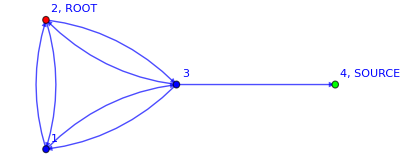
{-Graphics-,3,4}

```mathematica
graph
```

```mathematica
fields={ϕ,ψ,χ,ξ};
endTime=1;
replicas=1;
exp=ModExpectationValue[Z ,"graph"->graph[[1]],"oldSource"->graph[[2]],"newSource"->graph[[3]],"endTime"->endTime,"fields"->fields,"replicas"->replicas]//.δruleExternal
```

################### Operators found  ##################

σ+(σ^2 β_(1,3) β_(3,1))/((β_(1,2)+β_(1,3)) (σ+β_(3,1)+β_(3,2))^2)+(σ β_(1,3)^2 β_(3,1)^2)/((β_(1,2)+β_(1,3))^2 (σ+β_(3,1)+β_(3,2))^2)-σ^2/(σ+β_(3,1)+β_(3,2))-(2 σ β_(1,3) β_(3,1))/((β_(1,2)+β_(1,3)) (σ+β_(3,1)+β_(3,2)))

```mathematica
exp=Limit[exp,σ->∞]
```

(β_(1,2)^2 β_(3,1)+β_(1,2) β_(1,3) β_(3,1)+β_(1,2)^2 β_(3,2)+2 β_(1,2) β_(1,3) β_(3,2)+β_(1,3)^2 β_(3,2))/(β_(1,2)^2+2 β_(1,2) β_(1,3)+β_(1,3)^2)

```mathematica
exp//.β[a_,b_]/;(a<b):>β[b,a]
%//.(c_*a_^2+2c_ a_ b_ + c_ b_^2->HoldForm[c(a+b)^2])//.(a_^2+2 a_ b_  +b_^2->HoldForm[(a+b)^2])
```

(β_(2,1)^2 β_(3,1)+β_(2,1) β_(3,1)^2+β_(2,1)^2 β_(3,2)+2 β_(2,1) β_(3,1) β_(3,2)+β_(3,1)^2 β_(3,2))/(β_(2,1)^2+2 β_(2,1) β_(3,1)+β_(3,1)^2)

(β_(3,2) (β_(2,1)+β_(3,1))^2+β_(2,1)^2 β_(3,1)+β_(2,1) β_(3,1)^2)/(β_(2,1)+β_(3,1))^2

Easier case that we can compute: CORRECT!!!!!!

```mathematica
Z= Op[σ  (-Subscript[SuperStar[χ], 3,Subscript[t, 1],Subscript[1, 1],Subscript[m, 1]]+Subscript[SuperStar[χ], 4,Subscript[t, 1],Subscript[1, 1],Subscript[m, 1]])Subscript[χ, 4,Subscript[t, 1],Subscript[1, 1],Subscript[m, 1]]] Op[σ  (-Subscript[SuperStar[χ], 3,Subscript[t, 1],Subscript[1, 2],Subscript[m, 2]]+Subscript[SuperStar[χ], 4,Subscript[t, 1],Subscript[1, 2],Subscript[m, 2]])Subscript[χ, 4,Subscript[t, 1],Subscript[1, 2],Subscript[m, 2]]]V[1+(Subscript[R, 3,1,RGBColor[1, 1, 0]] Subscript[β, 3,1] Subscript[χ, 3,Subscript[t, 1],Subscript[i, 3],Subscript[m, 1]] Subscript[SuperStar[χ], 1,Subscript[t, 1],Subscript[i, 3],Subscript[m, 1]])/(Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4])+(Subscript[R, 3,2,RGBColor[1, 1, 0]] Subscript[β, 3,2] Subscript[χ, 3,Subscript[t, 1],Subscript[i, 3],Subscript[m, 1]] Subscript[SuperStar[χ], 2,Subscript[t, 1],Subscript[i, 3],Subscript[m, 1]])/(Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4])+(Subscript[R, 3,4,RGBColor[1, 1, 0]] Subscript[β, 3,4] Subscript[χ, 3,Subscript[t, 1],Subscript[i, 3],Subscript[m, 1]] Subscript[SuperStar[χ], 4,Subscript[t, 1],Subscript[i, 3],Subscript[m, 1]])/(Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4])+Subscript[ψ, 3,Subscript[t, 1],Subscript[j, 3],Subscript[m, 1]] Subscript[SuperStar[ψ], 3,Subscript[t, 2],Subscript[j, 3],Subscript[m, 1]]] V[1+(Subscript[R, 3,1,RGBColor[1, 1, 0]] Subscript[β, 3,1] Subscript[χ, 3,Subscript[t, 1],Subscript[i, 3],Subscript[m, 2]] Subscript[SuperStar[χ], 1,Subscript[t, 1],Subscript[i, 3],Subscript[m, 2]])/(Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4])+(Subscript[R, 3,2,RGBColor[1, 1, 0]] Subscript[β, 3,2] Subscript[χ, 3,Subscript[t, 1],Subscript[i, 3],Subscript[m, 2]] Subscript[SuperStar[χ], 2,Subscript[t, 1],Subscript[i, 3],Subscript[m, 2]])/(Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4])+(Subscript[R, 3,4,RGBColor[1, 1, 0]] Subscript[β, 3,4] Subscript[χ, 3,Subscript[t, 1],Subscript[i, 3],Subscript[m, 2]] Subscript[SuperStar[χ], 4,Subscript[t, 1],Subscript[i, 3],Subscript[m, 2]])/(Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4])+Subscript[ψ, 3,Subscript[t, 1],Subscript[j, 3],Subscript[m, 2]] Subscript[SuperStar[ψ], 3,Subscript[t, 2],Subscript[j, 3],Subscript[m, 2]]];
fields={χ,ψ};
endTime=1;
ModWickContraction[Z ,"endTime"->endTime,"fields"->fields,"replicas"->2]//.δruleExternal
```

################### Operators found  ##################

σ^2+(σ^2 R_(3,4,RGBColor[1, 1, 0])^2 β_(3,4)^2)/(β_(3,1)+β_(3,2)+β_(3,4))^2-(2 σ^2 R_(3,4,RGBColor[1, 1, 0]) β_(3,4))/(β_(3,1)+β_(3,2)+β_(3,4))

```mathematica
Limit[%/.Subscript[β, 3,4]->σ,σ->∞]
```

∞ (1-2 R_(3,4,RGBColor[1, 1, 0])+R_(3,4,RGBColor[1, 1, 0])^2)

```mathematica
Subscript[β, 3,1]^2+2 Subscript[β, 3,1] Subscript[β, 3,2]+Subscript[β, 3,2]^2//.(a_^2+2a_ b_ + b_^2->(a+b)^2)/.(a__)^2->(a)^-1
```

1/(β_(3,1)+β_(3,2))

```mathematica
(*CORRECT!!!!!!*)
```

## I would like to compute the denominator of the DLA transition probability. To do this, I try to use nn different fields and then send nn->-1.

```mathematica
fields={χ,ϕ};
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];
g=AugmentedGraph[g];

endTime=1;Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}]
```

V[1+ϕ_(1,t_2,0)] V[1+ϕ_(1,t_2,k_1)] V[1+ϕ_(2,t_2,0)] V[1+ϕ_(2,t_2,k_2)] V[1+ϕ_(3,t_2,0)] V[1+ϕ_(3,t_2,k_3)] V[1+ϕ_(4,t_2,0)] V[1+ϕ_(4,t_2,k_4)] V[1+χ_(4,t_1,1)] V[1+ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1)+R_(1,2,RGBColor[1, 0, 0]) β_(1,2) ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (χ^*)_(2,t_1,1)+(R_(1,2,RGBColor[0, 0, 1]) β_(1,2) χ_(1,t_1,i_1) (χ^*)_(2,t_1,i_1))/(β_(1,2)+β_(1,3))+R_(1,3,RGBColor[1, 0, 0]) β_(1,3) ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (χ^*)_(3,t_1,1)+(R_(1,3,RGBColor[0, 0, 1]) β_(1,3) χ_(1,t_1,i_1) (χ^*)_(3,t_1,i_1))/(β_(1,2)+β_(1,3))] V[1+ϕ_(2,t_1,k_2) (ϕ^*)_(2,t_2,k_2)+R_(2,1,RGBColor[1, 0, 0]) β_(2,1) ϕ_(2,t_1,k_2) (ϕ^*)_(1,t_2,k_2) (ϕ^*)_(2,t_2,k_2) (χ^*)_(1,t_1,1)+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) χ_(2,t_1,i_2) (χ^*)_(1,t_1,i_2))/(β_(2,1)+β_(2,3))+R_(2,3,RGBColor[1, 0, 0]) β_(2,3) ϕ_(2,t_1,k_2) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(3,t_2,k_2) (χ^*)_(3,t_1,1)+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) χ_(2,t_1,i_2) (χ^*)_(3,t_1,i_2))/(β_(2,1)+β_(2,3))] V[1+ϕ_(3,t_1,k_3) (ϕ^*)_(3,t_2,k_3)+R_(3,1,RGBColor[1, 0, 0]) β_(3,1) ϕ_(3,t_1,k_3) (ϕ^*)_(1,t_2,k_3) (ϕ^*)_(3,t_2,k_3) (χ^*)_(1,t_1,1)+(R_(3,1,RGBColor[0, 0, 1]) β_(3,1) χ_(3,t_1,i_3) (χ^*)_(1,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))+R_(3,2,RGBColor[1, 0, 0]) β_(3,2) ϕ_(3,t_1,k_3) (ϕ^*)_(2,t_2,k_3) (ϕ^*)_(3,t_2,k_3) (χ^*)_(2,t_1,1)+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) χ_(3,t_1,i_3) (χ^*)_(2,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))+R_(3,4,RGBColor[1, 0, 0]) β_(3,4) ϕ_(3,t_1,k_3) (ϕ^*)_(3,t_2,k_3) (ϕ^*)_(4,t_2,k_3) (χ^*)_(4,t_1,1)+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) χ_(3,t_1,i_3) (χ^*)_(4,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))]

```mathematica
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)))-(β_(1,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(1,2) β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(1,3) β_(2,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))

```mathematica
ExpectationValue[Z Op[(χs[4,Subscript[t, 1],1]-χs[3,Subscript[t, 1],1])]Op[(χs[4,Subscript[t, 1],1]-χs[3,Subscript[t, 1],1])],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

0

```mathematica
fields={χ,ϕ};
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];
g=AugmentedGraph[g];

endTime=1;
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];

Z1=ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)))-(β_(1,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(1,2) β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(1,3) β_(2,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))

```mathematica
endTime=3;
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];
Z3=ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

1-(β_(1,2)^3 β_(2,1)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3)+(3 β_(1,2)^2 β_(2,1)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2)-(3 β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)))-(β_(1,3)^3 β_(3,1)^3)/((β_(1,2)+β_(1,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(β_(1,2)^3 β_(2,3)^3 β_(3,1)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2)^2 β_(1,3) β_(2,3)^2 β_(3,1)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2) β_(1,3)^2 β_(2,3) β_(3,1)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2)^2 β_(1,3) β_(2,1) β_(2,3)^2 β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2)^2 β_(2,3)^3 β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(6 β_(1,2) β_(1,3)^2 β_(2,1) β_(2,3) β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(6 β_(1,2) β_(1,3) β_(2,3)^2 β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3)^3 β_(2,1) β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3)^2 β_(2,3) β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2) β_(1,3)^2 β_(2,1)^2 β_(2,3) β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(6 β_(1,2) β_(1,3) β_(2,1) β_(2,3)^2 β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2) β_(2,3)^3 β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3)^3 β_(2,1)^2 β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(6 β_(1,3)^2 β_(2,1) β_(2,3) β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3) β_(2,3)^2 β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(β_(1,3)^3 β_(2,1)^3 β_(3,2)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3)^2 β_(2,1)^2 β_(2,3) β_(3,2)^3)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3) β_(2,1) β_(2,3)^2 β_(3,2)^3)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(β_(2,3)^3 β_(3,2)^3)/((β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)+(3 β_(1,3)^2 β_(3,1)^2)/((β_(1,2)+β_(1,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(3 β_(1,2)^3 β_(2,1) β_(2,3)^2 β_(3,1)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(6 β_(1,2)^2 β_(1,3) β_(2,1) β_(2,3) β_(3,1)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(3 β_(1,2)^2 β_(2,3)^2 β_(3,1)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(3 β_(1,2) β_(1,3)^2 β_(2,1) β_(3,1)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)+(6 β_(1,2) β_(1,3) β_(2,3) β_(3,1)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)-(6 β_(1,2)^2 β_(1,3) β_(2,1)^2 β_(2,3) β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(6 β_(1,2)^2 β_(2,1) β_(2,3)^2 β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(6 β_(1,2) β_(1,3)^2 β_(2,1)^2 β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(6 β_(1,2) β_(2,3)^2 β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(6 β_(1,3)^2 β_(2,1) β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)+(6 β_(1,3) β_(2,3) β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)-(3 β_(1,2) β_(1,3)^2 β_(2,1)^3 β_(3,2)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(6 β_(1,2) β_(1,3) β_(2,1)^2 β_(2,3) β_(3,2)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(3 β_(1,2) β_(2,1) β_(2,3)^2 β_(3,2)^2)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(3 β_(1,3)^2 β_(2,1)^2 β_(3,2)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(6 β_(1,3) β_(2,1) β_(2,3) β_(3,2)^2)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(3 β_(2,3)^2 β_(3,2)^2)/((β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(3 β_(1,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,2)^3 β_(2,1)^2 β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,2)^2 β_(1,3) β_(2,1)^2 β_(3,1))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))+(6 β_(1,2)^2 β_(2,1) β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))+(6 β_(1,2) β_(1,3) β_(2,1) β_(3,1))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,2) β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,2)^2 β_(1,3) β_(2,1)^3 β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,2)^2 β_(2,1)^2 β_(2,3) β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4)))+(6 β_(1,2) β_(1,3) β_(2,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))+(6 β_(1,2) β_(2,1) β_(2,3) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,3) β_(2,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))

```mathematica
Z1^3-Z3//FullSimplify
```

0

```mathematica
(*SO, USING nn TIME-SLICES YIELDS Z^nn!!!! THIS IS EXPECTED. DOES IT WORK FOR <χ^*χ>?? *)
```

Does it work for <χ^*χ>?

###################  Operator found  ##################

{{1/12,{1,3,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]}},{1/6,{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]}}}

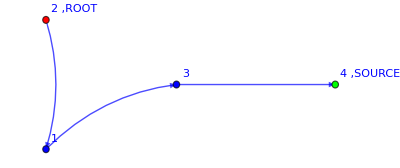

Weight==1/12

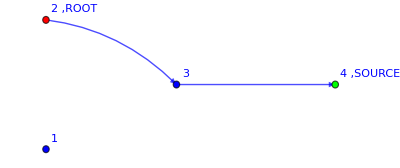

Weight==1/6

(β_(1,3) β_(2,1) β_(3,4))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))+(β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))

```mathematica
fields={χ,ϕ};
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];
g=AugmentedGraph[g];

endTime=1;
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];

Z1=ExpectationValue[Z Op[χs[2,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->True,"graph"->g]
```

```mathematica
endTime=3;
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];
Z3=ExpectationValue[Z Op[χs[2,Subscript[t, 1],1]] Op[χs[2,Subscript[t, 2],1]] Op[χs[2,Subscript[t, 3],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

(β_(1,3)^3 β_(2,1)^3 β_(3,4)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)+(3 β_(1,3)^2 β_(2,1)^2 β_(2,3) β_(3,4)^3)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)+(3 β_(1,3) β_(2,1) β_(2,3)^2 β_(3,4)^3)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)+(β_(2,3)^3 β_(3,4)^3)/((β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)

```mathematica
Z1^3-Z3//FullSimplify
```

0

```mathematica
(*IT WORKS!!!!!!!!!!!
CAN I USE THIS TO COMPUTE THE DENOMINATOR?????*)
```

Other attempt

```mathematica
Z=V[1+(Subscript[R, 1,2,RGBColor[0, 0, 1]] Subscript[β, 1,2] Subscript[χ, 1,Subscript[t, 1],Subscript[i, 1]] Subscript[SuperStar[χ], 2,Subscript[t, 1],Subscript[i, 1]])/(Subscript[β, 1,2]+Subscript[β, 1,3])+(Subscript[R, 1,3,RGBColor[0, 0, 1]] Subscript[β, 1,3] Subscript[χ, 1,Subscript[t, 1],Subscript[i, 1]] Subscript[SuperStar[χ], 3,Subscript[t, 1],Subscript[i, 1]])/(Subscript[β, 1,2]+Subscript[β, 1,3])] V[1+(Subscript[R, 2,1,RGBColor[0, 0, 1]] Subscript[β, 2,1] Subscript[χ, 2,Subscript[t, 1],Subscript[i, 2]] Subscript[SuperStar[χ], 1,Subscript[t, 1],Subscript[i, 2]])/(Subscript[β, 2,1]+Subscript[β, 2,3])+(Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[β, 2,3] Subscript[χ, 2,Subscript[t, 1],Subscript[i, 2]] Subscript[SuperStar[χ], 3,Subscript[t, 1],Subscript[i, 2]])/(Subscript[β, 2,1]+Subscript[β, 2,3])] V[1+(Subscript[R, 3,1,RGBColor[0, 0, 1]] Subscript[β, 3,1] Subscript[χ, 3,Subscript[t, 1],Subscript[i, 3]] Subscript[SuperStar[χ], 1,Subscript[t, 1],Subscript[i, 3]])/(Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4])+(Subscript[R, 3,2,RGBColor[0, 0, 1]] Subscript[β, 3,2] Subscript[χ, 3,Subscript[t, 1],Subscript[i, 3]] Subscript[SuperStar[χ], 2,Subscript[t, 1],Subscript[i, 3]])/(Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4])+(Subscript[R, 3,4,RGBColor[0, 0, 1]] Subscript[β, 3,4] Subscript[χ, 3,Subscript[t, 1],Subscript[i, 3]] Subscript[SuperStar[χ], 4,Subscript[t, 1],Subscript[i, 3]])/(Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4])];Z=Z/.χ[a_,b_,c_]->(ϕ[a,b,c])/.χs[a_,b_,c_]->ϕs[a,b,c]
```

V[1+(R_(1,2,RGBColor[0, 0, 1]) β_(1,2) ϕ_(1,t_1,i_1) (ϕ^*)_(2,t_1,i_1))/(β_(1,2)+β_(1,3))+(R_(1,3,RGBColor[0, 0, 1]) β_(1,3) ϕ_(1,t_1,i_1) (ϕ^*)_(3,t_1,i_1))/(β_(1,2)+β_(1,3))] V[1+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) ϕ_(2,t_1,i_2) (ϕ^*)_(1,t_1,i_2))/(β_(2,1)+β_(2,3))+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) ϕ_(2,t_1,i_2) (ϕ^*)_(3,t_1,i_2))/(β_(2,1)+β_(2,3))] V[1+(R_(3,1,RGBColor[0, 0, 1]) β_(3,1) ϕ_(3,t_1,i_3) (ϕ^*)_(1,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) ϕ_(3,t_1,i_3) (ϕ^*)_(2,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) ϕ_(3,t_1,i_3) (ϕ^*)_(4,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))]

```mathematica
fields={χ,ϕ};
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]-(1-(Subscript[β, 1,2] Subscript[β, 2,1])/((Subscript[β, 1,2]+Subscript[β, 1,3]) (Subscript[β, 2,1]+Subscript[β, 2,3]))-(Subscript[β, 1,3] Subscript[β, 3,1])/((Subscript[β, 1,2]+Subscript[β, 1,3]) (Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4]))-(Subscript[β, 1,2] Subscript[β, 2,3] Subscript[β, 3,1])/((Subscript[β, 1,2]+Subscript[β, 1,3]) (Subscript[β, 2,1]+Subscript[β, 2,3]) (Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4]))-(Subscript[β, 1,3] Subscript[β, 2,1] Subscript[β, 3,2])/((Subscript[β, 1,2]+Subscript[β, 1,3]) (Subscript[β, 2,1]+Subscript[β, 2,3]) (Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4]))-(Subscript[β, 2,3] Subscript[β, 3,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]) (Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4])))^2//FullSimplify
```

###################  Partition Function  ##################

(2 β_(1,3)^2 β_(3,2) (-2 β_(2,3) (β_(2,1)+β_(2,3)) β_(3,1)-β_(2,1)^2 β_(3,2))-2 β_(1,2)^2 β_(2,3) (β_(2,3) β_(3,1)^2+2 β_(2,1) β_(3,2) (β_(3,1)+β_(3,2)+β_(3,4)))-4 β_(1,2) β_(1,3) β_(2,3) β_(3,2) (β_(2,3) β_(3,1)+β_(2,1) (3 β_(3,1)+β_(3,2)+β_(3,4))))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)